## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="PYK";
```

```mathematica
Import["../../EnzymeBuildingBlocks/initializeNotebook.m"]
```

working dir:/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/

## Import Data From Database

```mathematica
desiredComplex=6737;
Import["../../EnzymeBuildingBlocks/importFromDB.m"]
```

unique_name | id
PKI-COMPLEX
PKII-CPLX | 5755
6737

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
(*Print Available Reaction/Protein Data*)
rxn
bindingMech[[1,8;;9]]//TableForm
#[[3;;4]]&/@complexData[[1]]//TableForm

(*Print Available Kinetic Data*)
{{"Km Values:","(kmList)"},
{"Substrate","Km_Value","CoSubstrate","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~kmList//TableForm
{{"S0.5 Values:","(s05List)"},
{"Substrate","S0.5_Value","CoSubstrate","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~s05List//TableForm
{{"kcat Values:","(kcatList)"},
{"Metabolite(s)","Value","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~kcatList//TableForm
{{"Inhibition Values:","(inhibitionList)"},
{"Parameter_Type","Inhibitor","Value","Inhibition Type","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~inhibitionList//TableForm
{{"Activation Values:","(activationList)"},
{"Parameter_Type","Activator","Value","Activation Type","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~activationList//TableForm
{{"Other Parameters:","(otherParms)"},
{"Parameter_Type","Metabolite","Value","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~otherParms//TableForm
```

(adp^c+h^c+pep^c→atp^c+pyr^c)^PYK

Part::partw: Part 1 of {} does not exist.

{}⟦1,8;;9⟧

Structure | 4

Km Values: | (kmList) |  |  |  |  |  | 
Substrate | Km_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
pep | 0.00011 | amp | 0.001
adp | 0.002 | M | 7 | 28. | trisac | 0.05 | mg2 | 0.005
cl | 0.01
cl | 0.05
k | 0.05
pep | 0.7 | adp | 0.002 | Null | 7 | 28. | trisac | 0.05 | mg2 | 0.005
cl | 0.01
cl | 0.05
k | 0.05

S0.5 Values: | (s05List) |  |  |  |  |  | 
Substrate | S0.5_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values: | (kcatList) |  |  |  |  | 
Metabolite(s) | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values: | (inhibitionList) |  |  |  |  |  |  | 
Parameter_Type | Inhibitor | Value | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values: | (activationList) |  |  |  |  |  |  | 
Parameter_Type | Activator | Value | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters: | (otherParms) |  |  |  |  |  | 
Parameter_Type | Metabolite | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Construct enzyme module

```mathematica
catalyticBranch={"E_PYK2[c] + adp[c] <=> E_PYK2[c]&adp",
"E_PYK2[c] + pep[c] <=> E_PYK2[c]&pep",
"E_PYK2[c]&pep + adp[c] <=> E_PYK2[c]&pep&adp",
"E_PYK2[c]&adp + pep[c] <=> E_PYK2[c]&pep&adp",
"E_PYK2[c]&pep&adp <=> E_PYK2[c]&pyr&atp",
"E_PYK2[c]&pyr&atp <=> E_PYK2[c]&pyr + atp[c]",
"E_PYK2[c]&pyr&atp <=> E_PYK2[c]&atp + pyr[c]",
"E_PYK2[c]&pyr <=> E_PYK2[c] + pyr[c]",
"E_PYK2[c]&atp <=> E_PYK2[c] + atp[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
```

#### Visualize Module (Optional)

{((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,((PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c)^PFK12,((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&f6p^c&atp^c)_^)^PFK13,((PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c)^PFK14,((PFK1^c&f6p^c&atp^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15,((PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c))^PFK11$3,((PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c)^PFK12$3,((PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c))^PFK13$3,((PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c)^PFK14$3,((PFK1^c&f6p^c&atp^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c))^PFK15$3,((PFK1^c)_^(gdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^c))^PFK11$7,((PFK1^c&fdp^c)_^(gdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^c)+fdp^c)^PFK12$7,((PFK1^c&f6p^c)_^(gdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c))^PFK13$7,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^c)+adp^c)^PFK14$7,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c))^PFK15$7,((PFK1^c)_^(gdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c))^PFK11$8,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^c)+fdp^c)^PFK12$8,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c))^PFK13$8,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)+adp^c)^PFK14$8,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c))^PFK15$8,((PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK11$10,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+fdp^c)^PFK12$10,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK13$10,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)+adp^c)^PFK14$10,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK15$10,((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$11,((PFK1^c)_^(gdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^c))^PFK1_Activation_gdp$12,((PFK1^c)_^(gdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^c))^PFK1_Activation_gdp$13,((PFK1^c)_^(gdp^cgdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Activation_gdp$14,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$15,((PFK1_T^c)_(pep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^c)^)^PFK1_Inhibition_pep$16,((PFK1_T^c)_(pep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^c)^)^PFK1_Inhibition_pep$17,((PFK1_T^c)_(pep^cpep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^)^PFK1_Inhibition_pep$18,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep}

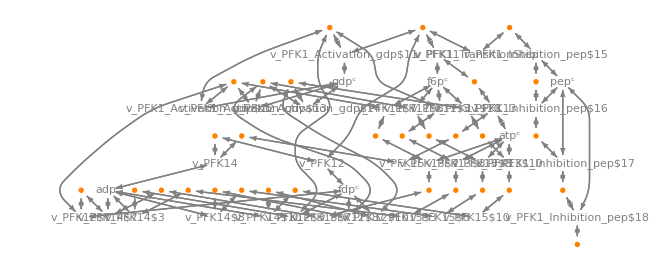

```mathematica
enzymeModel["Reactions"]
visualizePathways[enzymeModel](*Caution: Graphics can be unstable*)
enzymeModel;
```

### Setup King-Altmann Equations

#### Import and Define Dependencies

```mathematica
rNonModelMets[metList_]:=Delete[Delete[metList,Position[metList,h^c]],Position[metList,h2o^c]];(*h^c and h2o^c are not modeled*)
reverseZeroSub=#->0&/@rNonModelMets[getProducts[rxn]];
forwardZeroSub=#->0&/@rNonModelMets[getSubstrates[rxn]];
metSatForSub=#->∞&/@rNonModelMets[getSubstrates[rxn]];
metSatRevSub=#->∞&/@rNonModelMets[getProducts[rxn]];
rates=enzymeModel["Rates"]/.elem_[t]:>elem;
enzName=enzymeModel["Enzymes"][[1]]//getID//ToString;
KeqName=rxnName//ToString;
KeqVal=Keq[KeqName];
competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)

(*You could modify these, but you shouldn't unless you run into problems*)
volumeSub={parameter["Volume","c"]->1};
lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;
```

#### Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions

The transition indices are extracted based off of the sum of their mass action stoichiometry. Reactions with a sum of zero are assumed to be catalytic.

```mathematica
(*Initialize Lists*)
transitionID={};
allCatalyticReactions={};(*All Catalytic Reactions*)
nonCatalyticReactions={};(*All Other Reactions*)

(*Separate Catalytic and Non-Catalytic Reactions*)
If[StringMatchQ[#[[1]],RegularExpression[enzName<>"\\d+.*"]],(*If Reaction Name == "The Enzyme Name"<>+"A Number"*)
(*True: Reaction is Catalytic*)
AppendTo[allCatalyticReactions,#],
(*False: Reaction is Not Catalytic*)
AppendTo[nonCatalyticReactions,#]
]&/@enzymeModel["Reactions"];

(*Identify Transition Rate Equations*)
sumReactionStoich=Table[Total[getSignedStoich[allCatalyticReactions[[eqn]]]],{eqn,Length[allCatalyticReactions]}];
Do[If[sumReactionStoich[[eqn]] ==0,transitionID=Append[transitionID,allCatalyticReactions[[eqn]]//getID]],{eqn,Length[sumReactionStoich]}];

(*Extract Transition Rate Equations*)
transitionRateEqs={};
If[
MemberQ[transitionID,getID[Cases[#,_Keq,∞][[1]]]],
AppendTo[transitionRateEqs,#]
]&/@rates;
```

(*Double Check This Result*)

```mathematica
enzymeModel["Reactions"]
(*enzymeModel["Reactions"][[#]]&/@transitionID;*)
```

{((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,((PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c)^PFK12,((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&f6p^c&atp^c)_^)^PFK13,((PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c)^PFK14,((PFK1^c&f6p^c&atp^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15,((PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c))^PFK11$3,((PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c)^PFK12$3,((PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c))^PFK13$3,((PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c)^PFK14$3,((PFK1^c&f6p^c&atp^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c))^PFK15$3,((PFK1^c)_^(gdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^c))^PFK11$7,((PFK1^c&fdp^c)_^(gdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^c)+fdp^c)^PFK12$7,((PFK1^c&f6p^c)_^(gdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c))^PFK13$7,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^c)+adp^c)^PFK14$7,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c))^PFK15$7,((PFK1^c)_^(gdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c))^PFK11$8,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^c)+fdp^c)^PFK12$8,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c))^PFK13$8,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)+adp^c)^PFK14$8,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c))^PFK15$8,((PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK11$10,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+fdp^c)^PFK12$10,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK13$10,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)+adp^c)^PFK14$10,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK15$10,((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$11,((PFK1^c)_^(gdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^c))^PFK1_Activation_gdp$12,((PFK1^c)_^(gdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^c))^PFK1_Activation_gdp$13,((PFK1^c)_^(gdp^cgdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Activation_gdp$14,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$15,((PFK1_T^c)_(pep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^c)^)^PFK1_Inhibition_pep$16,((PFK1_T^c)_(pep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^c)^)^PFK1_Inhibition_pep$17,((PFK1_T^c)_(pep^cpep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^)^PFK1_Inhibition_pep$18,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep}

#### King-Altman Workaround Using Mathematica Solve Without Product Inhibition

This section of code will check to see if there is a 'absoluteFluxNoProdInhib.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation without competitive product inhibition (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the ‘absoluteFluxNoProdInhib.m’ file in this notebook’s current directory.

```mathematica
unifiedRateConstList=Flatten[{rateconst[getID[#],True]->unifyRateConstants[rateconst[getID[#],True]],rateconst[getID[#],False]->unifyRateConstants[rateconst[getID[#],False]]}&/@allCatalyticReactions];
unifiedRateConstList=Join[unifiedRateConstList,Flatten[{rateconst[getID[#],True]->unifyRateConstants[rateconst[getID[#],True]],rateconst[getID[#],False]->unifyRateConstants[rateconst[getID[#],False]]}&/@nonCatalyticReactions]];
```

```mathematica
(*If[
FileExistsQ[workingDir<>"enzSolNoProdInhib.m"]&&FileExistsQ[workingDir<>"absoluteFluxNoProdInhib.m"],
(*True: 'enzSolNoProdInhib.m' and 'absoluteFluxNoProdInhib.m' Exists*)
enzSolNoProdInhib=Import[workingDir<>"enzSolNoProdInhib.m"];
absoluteFluxNoProdInhib=Import[workingDir<>"absoluteFluxNoProdInhib.m"];,

(*False: 'enzSolNoProdInhib.m' and 'absoluteFluxNoProdInhib.m'  Do Not Exist*)
	(*Generate a System of Equations *)
fluxEq=(*unifyRateConstants[*)Total[transitionRateEqs];
fluxEq=keq2kHT[fluxEq]/.unifiedRateConstList(*]*);(*Flux Will Always Go through the Transition Step*)
enzForms=Cases[enzymeModel["Species"],_enzyme]//Union;
enzConservationEq=parameter["E_total"]==Total[enzForms];(*Enzyme Conservation Equation*)
enzPos=Flatten[Position[enzymeModel["Species"],_enzyme]];
ssEq=stripTime[enzymeModel["ODE"][[enzPos]]/._'[t]->0];(*Steady State Equations*)
ssEq=(*unifyRateConstants[*)keq2kHT[ssEq]/.unifiedRateConstList(*]*);

	(*Solve the System for Each Enzyme Form (This May Take Some Time)*)
enzSolNoProdInhib=anonymize[Solve[Join[ssEq,{enzConservationEq}],enzForms]];
enzSolNoProdInhib=keq2kHT[enzSolNoProdInhib[[1]]];

	(*Apply the Solution to the Flux Equation*)
absoluteFluxNoProdInhib=fluxEq/.enzSolNoProdInhib;(*In terms of E_total*)
absoluteFluxNoProdInhib=parameter["v",rxnName]->keq2kHT[
													anonymize[Simplify[
													absoluteFluxNoProdInhib
													]]
													];

	(*Cache the Results*)
Export[workingDir<>"enzSolNoProdInhib.m",enzSolNoProdInhib];
Export[workingDir<>"absoluteFluxNoProdInhib.m",absoluteFluxNoProdInhib];
];*)
```

```mathematica
Semi-Automated Add Competitive Inhibition Steps
```

```mathematica
(*
This block of code assembles competitive inhibition reactions to be added to the model. The reactions are appended to the 
'competitiveRxns' list, initialized above. Copy this cell for each competitive inhibitor you want to add. The reactions in 
'competitiveRxns' are added to the Enzyme Module, 'enzymeModel', in a separate cell below.
*)

(*USER INPUT----------------------------------------*)
inhibitorMet= {};
affectedMets={};(*There can be multiple metabolites*)
(*-------------------------------------------------*)

affectedRxns=Table[Select[allCatalyticReactions,MemberQ[Union[{getSubstrates[#],getProducts[#]}]~Flatten~1,met]&],{met,affectedMets}];
affectedEnzForms=Table[
If[
MemberQ[getSubstrates[rxn],affectedMets[[met]]],
(*True: Is a Reactant*)
#&/@Cases[getSubstrates[rxn],_enzyme,∞],
(*False: Is a Product*)
#&/@Cases[getProducts[rxn],_enzyme,∞]
],
{met,affectedMets//Length},{rxn,affectedRxns[[met]]}]//Flatten;

AppendTo[competitiveRxns,
Table[
r[enzName<>"_Competitive_"<>inhibitorMet[[1]]<>"_"<>ToString[enz],(*Reaction Name*)
{affectedEnzForms[[enz]],inhibitorMet},(*Substrates*)
{bindCatalytic[affectedEnzForms[[enz]],inhibitorMet]},(*Products*)
{1,1,1}](*Stoichiometry*),
{enz,affectedEnzForms//Length}]];
```

```mathematica
(*Evaluate This Cell*)
(*Equivalent Rate Constants*)
eqRateConstSub=Join[eqRateConstSub,rateconst[getID[#],True]->
rateconst[StringCases[getID[#],RegularExpression["(.*)_\\d+"]->"$1"][[1]],True]&/@
Flatten[competitiveRxns]]//Union;
eqRateConstSub=Join[eqRateConstSub,rateconst[getID[#],False]->
rateconst[StringCases[getID[#],RegularExpression["(.*)_\\d+"]->"$1"][[1]],False]&/@
Flatten[competitiveRxns]]//Union;
(*Add Competitive Reactions to the Enzyme Module*)
(*enzymeModel=addReactions[enzymeModel,Flatten[competitiveRxns]];
nonCatalyticReactions=Join[nonCatalyticReactions,competitiveRxns]//Flatten;
(*Print Reactions*)
enzymeModel["Reactions"]*)
```

#### King-Altman Workaround Using Mathematica Solve

This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the ‘absoluteFlux.m’ file in this notebook’s current directory.

```mathematica
If[FileExistsQ[workingDir<>"enzSol.m"]&&FileExistsQ[workingDir<>"absoluteFlux.m"],
(*True: 'enzSol.m' and 'absoluteFlux.m' Exists*)
enzSol=Import[workingDir<>"enzSol.m"];
absoluteFlux=Import[workingDir<>"absoluteFlux.m"];,

(*False: 'enzSol.m' and 'absoluteFlux.m'  Do Not Exist*)
	(*Generate a System of Equations *)
fluxEq=(*unifyRateConstants[*)Total[transitionRateEqs]/.unifiedRateConstList(*]*);(*Flux Will Always Go through the Transition Step*)
enzForms=Cases[enzymeModel["Species"],_enzyme]//Union;
enzConservationEq=parameter["E_total"]==Total[enzForms];(*Enzyme Conservation Equation*)
enzPos=Flatten[Position[enzymeModel["Species"],_enzyme]];
ssEq=stripTime[enzymeModel["ODE"][[enzPos]]/._'[t]->0];(*Steady State Equations*)
ssEq=(*unifyRateConstants*)keq2kHT[ssEq]/.unifiedRateConstList;

	(*Solve the System for Each Enzyme Form (This May Take Some Time)*)
enzSol=anonymize[Solve[Join[ssEq,{enzConservationEq}],enzForms]];
enzSol=keq2kHT[enzSol[[1]]];

	(*Apply the Solution to the Flux Equation*)
absoluteFlux=fluxEq/.enzSol;(*In terms of E_total*)
absoluteFlux=parameter["v",rxnName]->keq2kHT[
											anonymize[Simplify[
											absoluteFlux
											]]
											];

	(*Cache the Results*)
Export[workingDir<>"enzSol.m",enzSol];
Export[workingDir<>"absoluteFlux.m",absoluteFlux];
];
```

#### Equivalent Rate Constant Substitution for Random Ordered Mechanisms

This should work automatically, a substitution rule list is created with the name: ‘eqRateConstSub’. It is kind of a greedy section of code, so double check the results to make sure they’re accurate

```mathematica
(*Work Around for Added Competitive Reaction ID's*)
eqIDSub=Union[getID[#[[1]]]->getID[#[[2]]]&/@eqRateConstSub];

(*Catalytic Reactions*)
freeMetRxns=Cases[getSpecies[#],_metabolite,∞]&/@allCatalyticReactions;
allSubstrates=Cases[getSpecies[enzymeModel],_metabolite,∞];
equivalentRxns={};
Do[
AppendTo[equivalentRxns,{}],
{Length[allSubstrates]}];
(*Extract Equivalent Reactions*)
Table[
If[
SameQ[freeMetRxns[[rxn,1]],allSubstrates[[met]]],
AppendTo[equivalentRxns[[met]],rxn]];
freeMetRxns[[rxn,1]],
{met,Length[allSubstrates]},{rxn,Length[freeMetRxns]}]~Quiet~{Part::partw};
(*Parallel Catalytic Reactions Are Not Dealt with Using this Rule List*)
equivalentRxns=Table[{unifyRateConstants[getID[allCatalyticReactions[[#]]]],#}&/@rxnSet,{rxnSet,equivalentRxns}];
equivalentRxns=Table[
If[Length[DeleteDuplicates[rxnSet,#1[[1]]==#2[[1]]&]]>1,
DeleteDuplicates[rxnSet,#1[[1]]==#2[[1]]&][[All,2]],
{}
],
{rxnSet,equivalentRxns}];
(*Assemble Rule List and New 'rateconst' Names*)
equivalentRxnIDs=Table[
ToString[enzName]<>ToString[equivalentRxns[[eqSet,react]]],
{eqSet,Length[equivalentRxns]},{react,Length[equivalentRxns[[eqSet]]]}];
eqRateConst=Table[
StringJoin[Riffle[Map[ToString,Join[{enzName},equivalentRxns[[eqRxn]]]],"_"]],
{eqRxn,Length[equivalentRxns]}];
eqRateConst=Table[
rateconst[rate,If[boole==1,False,True]],
{rate,eqRateConst},{boole,2}];
indvRateConst=Table[
rateconst[equivalentRxnIDs[[eqSet,reactID]],If[boole==1,False,True]],
{eqSet,Length[equivalentRxnIDs]},{boole,2},{reactID,Length[equivalentRxnIDs[[eqSet]]]}];
eqRateConstSub=Join[eqRateConstSub,Flatten[
Table[
#->eqRateConst[[eqRate,direction]]&/@indvRateConst[[eqRate,direction]],{eqRate,Length[eqRateConst]},{direction,Length[eqRateConst[[eqRate]]]}]
]];

(*Non-Catalytic Reactions*)
freeMetRxns=Cases[getSpecies[#],_metabolite,∞]&/@nonCatalyticReactions;
allSubstrates=Cases[getSpecies[enzymeModel],_metabolite,∞];
equivalentRxns={};
Do[
AppendTo[equivalentRxns,{}],
{Length[allSubstrates]}];
(*Extract Equivalent Reactions*)
Table[
If[
SameQ[freeMetRxns[[rxn,1]],allSubstrates[[met]]],
AppendTo[equivalentRxns[[met]],rxn]];
freeMetRxns[[rxn,1]],
{met,Length[allSubstrates]},{rxn,Length[freeMetRxns]}]~Quiet~{Part::partw};
(*Parallel Catalytic Reactions Are Not Dealt with Using this Rule List*)
equivalentRxns=Table[{unifyRateConstants[getID[nonCatalyticReactions[[#]]]],#}&/@rxnSet,{rxnSet,equivalentRxns}]/.eqIDSub;
equivalentRxns=Table[
If[Length[DeleteDuplicates[rxnSet,#1[[1]]==#2[[1]]&]]>1,
DeleteDuplicates[rxnSet,#1[[1]]==#2[[1]]&][[All,2]],
{}
],
{rxnSet,equivalentRxns}];
(*Assemble Rule List and New 'rateconst' Names*)
equivalentRxnIDs=Table[
ToString[enzName]<>ToString[equivalentRxns[[eqSet,react]]],
{eqSet,Length[equivalentRxns]},{react,Length[equivalentRxns[[eqSet]]]}];
eqRateConst=Table[
StringJoin[Riffle[Map[ToString,Join[{enzName},equivalentRxns[[eqRxn]]]],"_"]],
{eqRxn,Length[equivalentRxns]}];
eqRateConst=Table[
rateconst[rate,If[boole==1,False,True]],
{rate,eqRateConst},{boole,2}];
indvRateConst=Table[
rateconst[equivalentRxnIDs[[eqSet,reactID]],If[boole==1,False,True]],
{eqSet,Length[equivalentRxnIDs]},{boole,2},{reactID,Length[equivalentRxnIDs[[eqSet]]]}];
eqRateConstSub=Join[eqRateConstSub,Flatten[
Table[
#->eqRateConst[[eqRate,direction]]&/@indvRateConst[[eqRate,direction]],{eqRate,Length[eqRateConst]},{direction,Length[eqRateConst[[eqRate]]]}]
]]//Union;
```

#### Assemble the Generalized Flux Equation and Derive a Substition of the Reverse Catalytic Rate Constant Using the Haldane Relation

```mathematica
absoluteFluxEqn=absoluteFlux[[2]];
absoluteFluxEqn=absoluteFluxEqn/.unifiedRateConstList/.eqRateConstSub;(*Equivalent Rate Constants*)

(*Product Inhibition Work-Around*)
(*absoluteFluxNoProdInhibEqn=absoluteFluxNoProdInhib[[2]];
absoluteFluxNoProdInhibEqn=absoluteFluxNoProdInhibEqn/.unifiedRateConstList/.eqRateConstSub;(*Equivalent Rate Constants*)*)

haldane=(*unifyRateConstants[*)haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneSubOutParameter=Table[Select[reverseConsts[enzymeModel],getID[#]==id&],{id,transitionID}]//Flatten;
haldaneSub=Quiet[Solve[haldane/.{haldane[[1]]->KeqVal},haldaneSubOutParameter[[1]]][[1]],{Solve::ratnz}];
haldaneSub=haldaneSub/.eqRateConstSub;(*Equivalent Rate Constants*)
```

#### Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data

Simplify fixes Python evaluation issues dealing with fractional exponents (e.g. ‘(-1)**(3/5)’ returns 1.0)

```mathematica
(*kcat Forward*)
absoluteRateForward=
Simplify[(absoluteFluxEqn/.reverseZeroSub/.volumeSub)/.haldaneSub];

(*kcat Reverse*)
absoluteRateReverse=
Simplify[(-absoluteFluxEqn/.forwardZeroSub/.volumeSub)/.haldaneSub];

(*Forward Km(s)*)
relativeRateForward=
Simplify[absoluteRateForward/(Limit[absoluteFluxEqn/.reverseZeroSub/.volumeSub,#]/.haldaneSub)]&/@metSatForSub;
(*Reverse Km(s)*)
relativeRateReverse=
Simplify[-absoluteRateReverse/(Limit[absoluteFluxEqn/.forwardZeroSub/.volumeSub,#]/.haldaneSub)]&/@metSatRevSub;
```

#### Assemble Rate Constant And Metabolite Substitutions for Export

```mathematica
finalRateConsts=
Variables[
Union[
Cases[
Join[{absoluteRateForward},{absoluteRateReverse},relativeRateForward,relativeRateReverse]//Flatten,
_rateconst,∞]]];
rateConstsSub=Thread[finalRateConsts->Table["x<"<>ToString[i]<>">",{i,0,Length[finalRateConsts]-1}]];

(*Extract All Metabolites*)
mets=Table[
{param[[7]],Select[param[[15]],#[[5]]≠"Buffer"&&#[[5]]≠"Salt"&&#[[5]]≠"Cofactor"&][[All,3]]},
{param, parameterData}]//Flatten//Union;
mets=Select[mets,#≠"Null"&];
char2met=#->m[#,"c"]&/@mets;
mets=mets/.char2met;
metsFull=Join[mets,Cases[enzymeModel,_metabolite,∞]]//Union;

(*Handle Metabolites for Export*)
finalMets=Join[metsFull,{Underscript[E_total, Global],parameter["pH"],parameter["Temp"]}];
finalMets=Prepend[finalMets,KeqVal];
metsSub=
Thread[finalMets->Table["d<"<>ToString[i]<>">",{i,0,Length[finalMets]-1}]];
```

### Manual Modifications Section

This section provides a space to manually modify your kinetic equations before they are exported.

#### None

### Export Equations

```mathematica
eqnNameList={"absRateFor",
			"absRateRev",
			Table["relRateFor_"<>ToString[satMet],{satMet,metSatForSub[[All,1,1]]}],
			Table["relRateRev_"<>ToString[satMet],{satMet,metSatRevSub[[All,1,1]]}]}//Flatten;

eqnValList={absoluteRateForward,
			absoluteRateReverse,
			Table[eqn,{eqn,relativeRateForward}],
			Table[eqn,{eqn,relativeRateReverse}]}//Flatten;

eqnValListPy=Table[eqn/.rateConstsSub/.metsSub//ToPython,{eqn,eqnValList}];

eqnList={eqnNameList,eqnValListPy,eqnValList};
fileList=Table[outputPath<>eqnname<>".txt",{eqnname,eqnList[[1]]}];
fileListSub=Table[fileList[[i]]->eqnValList[[i]],{i,1,Length[fileList]}];
Do[Export[fileList[[i]],eqnList[[2,i]]],{i,1,Length[eqnList[[2]]]}];
```

## Semi-Automated Simulate Data

### User Input Section

```mathematica
minPsDataVal[Km_]:=Log10[Km]-1;
maxPsDataVal[Km_]:=Log10[Km]+1;
logStepSize=0.2;
(*nonKmParamWeight=3;*)
nonKmParamWeight=Length[Table[1,{i,minPsDataVal[1],maxPsDataVal[1],logStepSize}]];(*Weighting factor for non-Km data points. You can be specify this manually*)
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
(**)
```

### Chemical Activity Correction (Optional)

If you want to use the actual metabolite concentrations for fitting and do not want to correct for chemical activities, SKIP THIS SECTION.
--This section of code uses eQuilibrator Data to assmeble equations that calculate the active charge-isomers concentrations for each metabolite based on assay conditions and the chemical activity coefficient.
--The overall chemical activity is calculated by this correction: γ * [S^z], where γ = chemical activity coefficient and [S^z] = the concentration of the active charge form of the metabolite. Skipping this section results in γ = 1 and [S^z] = [S]

#### Extract Data From eQuilibrator and Assemble/Handle Dependencies

This Cell extracts the thermodynamic dependencies from eQuilibrator and configures the variables and substitutions to calculate the charge-isomer concentrations of metabolites (e.g atp4-, atp3-, atp2- ...) and the chemical activity coefficient γ.

```mathematica
(*Pseudo Query Equilibrator for Metabolite Data*)
equilibratorInfo=Table[Select[bigg2equilibrator,getID[#[[1]]]==getID[met]&][[1]],{met,metsFull}];

(*Process the Equilibrator Data*)
equilibratorInfo=Table[
Sort[(*Sort by least to greatest nH*)
DeleteDuplicates[(*Delete by duplicate nH values (Preference is given to Alberty because it is first)*)
Flatten[equilibratorInfo[[met,2,All,3,2]],1],
#1[[2,2]]==#2[[2,2]]&],
#1[[2,2]]<#2[[2,2]]&],
{met,equilibratorInfo//Length}];
equilibratorInfo=Thread[metsFull->equilibratorInfo];
isomerMets=Table[(*Name the Pseudo-Isomers*)
m[getID[metsFull[[met]]]<>"("<>ToString[equilibratorInfo[[met,2,z,5,2]]]<>")","c"],
{met,Length[equilibratorInfo]},{z,Length[equilibratorInfo[[met,2]]]}];
nHSub=Table[
"nH_"<>getID[isomerMets[[met,z]]]->equilibratorInfo[[met,2,z,2,2]],
{met,Length[equilibratorInfo]},{z,Length[equilibratorInfo[[met,2]]]}];
chargeSub=Table[
"z_"<>getID[isomerMets[[met,z]]]->equilibratorInfo[[met,2,z,5,2]],
{met,Length[equilibratorInfo]},{z,Length[equilibratorInfo[[met,2]]]}];
isomerChargeSub=Table[
Thread[isomerMets[[met]]->chargeSub[[met,All,2]]],
{met,isomerMets//Length}];
(*Metabolite Related Thermodynamic Parameters Assembly*)
dGFormationVars=Table[
dGstd["f_"<>getID[isomerMets[[met,z]]]],
{met,Length[isomerMets]},{z,Length[isomerMets[[met]]]}];
dGFormationAdjustedVars=Table[
dGstd["f'_"<>getID[isomerMets[[met,z]]]],
{met,Length[isomerMets]},{z,Length[isomerMets[[met]]]}];
dGFormationVals=Table[(*From Equilibrator*)
If[equilibratorInfo[[met,2,z,1,2]]==0,
(*True: Database Value is zero (i.e. does not have units)*)
dGFormationVars[[met,z]]->equilibratorInfo[[met,2,z,1,2]],
(*False: Database Value is not zero (i.e. has units)*)
dGFormationVars[[met,z]]->equilibratorInfo[[met,2,z,1,2,1]]
],
{met,Length[isomerMets]},{z,Length[isomerMets[[met]]]}];

(*dGFormationVals=Table[(*From Equilibrator*)
dGFormationVars[[met,z]]->equilibratorInfo[[met,2,z,1,2,1]],
{met,Length[isomerMets]},{z,Length[isomerMets[[met]]]}];*)

(* The adjusted delta_G of formation is represented by the following equation:
Subscript[ΔG, f'_j]^∘ = Subscript[ΔG, Subscript[f, j]]^∘ + Subscript[nH, j]*R*T*ln(10)*pH - (2.91482*(Subscript[Z, j] - Subscript[nH, j])*I^(1/2))/(1 +1.6*I^(1/2)),
	where: Subscript[nH, j] = Number of hydrogen atoms in species j  ;
			Subscript[Z, j] = Charge number of species j  ;
			R = 8.314472 Joule Kelvin^-1 Mole^-1  ;
			T = 298.15 Kelvin  ;
			I = Ionic Strength  ;
*)
dGFormationAdjustedVarsSub=Table[
dGFormationAdjustedVars[[met,charge]]-> 
dGFormationVars[[met,charge]]+nHSub[[met,charge,1]]*MolarGasConstant[[1]]*298.15*Log[10]*parameter["pH"]-(2.91482*(chargeSub[[met,charge,1]]^2-nHSub[[met,charge,1]])*parameter["IonicStrength"]^(1/2)/(1+1.6*parameter["IonicStrength"]^(1/2))),
{met,Length[isomerMets]},{charge,Length[isomerMets[[met]]]}];
(*Keq Related Thermodynamic Parameters Assembly*)
(*Keq Variable Names*)
isomerKeqVars=Table[
Keq[getID[metsFull[[met]]]<>"("<>ToString[equilibratorInfo[[met,2,z-1,5,2]]]<>"<=>"<>ToString[equilibratorInfo[[met,2,z,5,2]]]<>")"],{met,Length[equilibratorInfo]},{z,2,Length[equilibratorInfo[[met,2]]]}];
(*delta_G reaction Names*)
dGReactions=Table[
dGstd["r_"<>getID[isomerKeqVars[[met,react]]]],
{met,Length[isomerKeqVars]},{react,Length[isomerKeqVars[[met]]]}];
(* 
The reaction delta_G is represented by the following equation:
Subscript[ΔG, r(j-1<=>j)]^∘ = Subscript[ΔG, f'_j]^∘ - Subscript[ΔG, f'_(j - 1)]^∘       
*)
dGReactionsSub=Table[
dGReactions[[met,react]]->dGFormationAdjustedVars[[met,react+1]]-dGFormationAdjustedVars[[met,react]],
{met,Length[dGReactions]},{react,Length[dGReactions[[met]]]}];
(* 
The pseudo-Isomer Keq is represented by the following equation:
Keq = exp(-Subscript[ΔG, r(j-1<=>j)]^∘/(R*T))  ,

     where:  R = 8.314472 Joule Kelvin^-1 Mole^-1  
	T = 298.15 Kelvin  ;
*)
isomerKeqSub=Table[isomerKeqVars[[met,react]]->Exp[(-1*dGReactions[[met,react]])/(298.15*MolarGasConstant[[1]])],{met,Length[isomerKeqVars]},{react,Length[isomerKeqVars[[met]]]}];
```

#### Assemble and Process the Pseudo-Isomer Equations

This cell evaluates the fractional abundance of each charge isomer at in vivo pH and Ionic Strength (Specified in the User Inputs section). The active charge isomer is guessed to be the most abundant form at in vivo conditions

```mathematica
(*Assemble Pseudo Isomer Equations*)
keqEqns=Table[isomerKeqVars[[met,react]]==isomerMets[[met,react+1]]/isomerMets[[met,react]],{met,Length[isomerKeqVars]},{react,Length[isomerKeqVars[[met]]]}];
conservationEqn=Table[{metsFull[[met]]==Total[isomerMets[[met]]]},{met,Length[metsFull]}];
pIsomerEqns=Table[Join[keqEqns[[met]],conservationEqn[[met]]],{met,keqEqns//Length}];

(*Substitute in Corrections and Data Values*)
pIsomerEqnsFull=
Table[
pIsomerEqns[[met]]/.
isomerKeqSub[[met]]/.
	dGReactionsSub[[met]]/.
		dGFormationAdjustedVarsSub[[met]]/.
			dGFormationVals[[met]]/.
				chargeSub[[met]]/.
					nHSub[[met]]/.
						parameter["pH"]->inVivoPH/.
							parameter["IonicStrength"]->inVivoIS/.
								Thread[metsFull->1],
{met,pIsomerEqns//Length}];

(*Solve for the Pseudo Isomer Concentrations*)
inVivoConc=Table[
Quiet[Solve[
pIsomerEqnsFull[[met]],isomerMets[[met]]
],{Solve::ratnz}][[1]],
{met,isomerMets//Length}];

(*Sort Concentrations by Largest to Smallest*)
inVivoConc=Table[Sort[inVivoConc[[met]],#1[[2]]>#2[[2]]&],{met,inVivoConc//Length}];
"Calculated Fraction of in vivo Concentrations:"
inVivoConc
"Estimated Active Forms:"
activeIsomerForms=Thread[metsFull->inVivoConc[[All,1,1]]]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0., 0., 2.57006×10^8, -8.12408×10^7, 0.}, {0., 6.59968×10^9, -1.75826×10^6, 0., 0.}, {5.82067×10^10, -10575., 0., 0., 0.}, {1., 1., 1., 1., -1.}} may contain significant numerical errors.

Calculated Fraction of in vivo Concentrations:

{{(adp(-3))^c→0.67776,(adp(-2))^c→0.321996,(adp(-1))^c→0.000232309,(adp(-4))^c→0.0000110907,(adp(0))^c→2.22276×10^-7,(adp(-5))^c→3.74885×10^-12,(adp(1))^c→3.12944×10^-12,(adp(2))^c→5.06793×10^-18},{(atp(-3))^c→0.556017,(atp(-4))^c→0.44298,(atp(-2))^c→0.000835352,(atp(-5))^c→0.000161925,(atp(-1))^c→5.01197×10^-6,(atp(0))^c→1.06709×10^-10,(atp(1))^c→6.87006×10^-16,(atp(2))^c→1.60982×10^-22},{(f6p(-2))^c→0.943566,(f6p(-1))^c→0.0557297,(f6p(-3))^c→0.000704269,(f6p(0))^c→1.22036×10^-8,(f6p(-4))^c→4.22396×10^-9,(f6p(-5))^c→1.39529×10^-15},{(fdp(-4))^c→0.867431,(fdp(-3))^c→0.122292,(fdp(-5))^c→0.00595294,(fdp(-2))^c→0.00432447,(fdp(-6))^c→3.41422×10^-8,(fdp(-1))^c→9.50019×10^-9,(fdp(0))^c→2.32793×10^-15},{(gdp(-3))^c→0.559346,(gdp(-2))^c→0.439389,(gdp(-4))^c→0.00124245,(gdp(-1))^c→0.0000219059,(gdp(-5))^c→1.38803×10^-8,(gdp(0))^c→6.2983×10^-11,(gdp(-6))^c→4.69485×10^-15,(gdp(1))^c→4.35013×10^-17},{(pep(-3))^c→0.75977,(pep(-2))^c→0.240166,(pep(-1))^c→0.0000639842,(pep(0))^c→1.16247×10^-11}}

Estimated Active Forms:

{adp^c→(adp(-3))^c,atp^c→(atp(-3))^c,f6p^c→(f6p(-2))^c,fdp^c→(fdp(-4))^c,gdp^c→(gdp(-3))^c,pep^c→(pep(-3))^c}

#### Manually Specify Active Isomer Forms (Optional)

If you know the actual active charge-isomer, you can specify it here. Note: the whole ‘activeIsomerForms’ list needs to be respecified here.

```mathematica
(*activeIsomerForms={adp^c->(adp(-2))^c,atp^c->(atp(-2))^c,f6p^c->(f6p(-2))^c,fdp^c->(fdp(-4))^c,gdp^c->(gdp(-2))^c,pep^c->(pep(-3))^c};*)
```

#### Set Up Equations for Calculating Pseudo-Isomer Concentrations

Equations calculating the concentration of the active charge-isomer are assembled here. Each equation is a function of: Ionic Strength, pH, and metabolite concentration.

```mathematica
(*Substitute in Corrections and Data Values without the in vivo Assumptions*)
pIsomerEqnsSub=
Table[
pIsomerEqns[[met]]/.
isomerKeqSub[[met]]/.
	dGReactionsSub[[met]]/.
		dGFormationAdjustedVarsSub[[met]]/.
			dGFormationVals[[met]]/.
				chargeSub[[met]]/.
					nHSub[[met]],
{met,pIsomerEqns//Length}];
(*Symbolically Solve for the Pseudo-Isomer Forms*)
isoFormEqns=Table[
Solve[pIsomerEqnsSub[[met]],isomerMets[[met]]][[1]],
{met,isomerMets//Length}];
(*Remove the Active Pseudo-Isomer Form*)
isoForm=Table[
Delete[
isoFormEqns[[met]],Position[
isoFormEqns[[met,All,1]],activeIsomerForms[[met,2]]]],
{met,isomerMets//Length}];
(*Substitute the Equations Back into the Conservation Equation*)
activeIsoFormEqns=Table[
pIsomerEqnsSub[[met,-1]]/.isoForm[[met]],
{met,pIsomerEqnsSub//Length}];
(*Equations that Solve for the Active Isoform Concentration*)
activeIsoSub=Table[
Solve[activeIsoFormEqns[[met]],activeIsomerForms[[met,2]]],
{met,activeIsomerForms//Length}]//Flatten;
```

#### Activity Coefficient Calculation Using the Extended Debye-Huckel Equation

γ = (0.5085*z^2*√IonicStrength)/(1 + 0.3281*a*√IonicStrength), where a is the effective diameter of the ion

```mathematica
debyeHuckelEq[z_,a_]:=(0.5085*z^2*Sqrt[parameter["IonicStrength"]])/(1+0.3281*a*Sqrt[parameter["IonicStrength"]]);
(*Assemble Equations*)
chargeVals=Thread[activeIsomerForms[[All,2]]/.Flatten[isomerChargeSub]];
activityCoefficient=
Thread[(* γ values*)
activeIsomerForms[[All,2]]->
Table[
debyeHuckelEq[met,effectiveIonDiameter],
{met,chargeVals}]];
```

### Data For Km’s

```mathematica
(*Michaelis-Menten Equation*)
kmEqn[S_,Km_]:=S/(Km+S);

(*Change Character Metabolite Names Into MASS toolbox Metabolite Notation. 
NOTE: You may have to add some metabolites in for unusual assay conditions*)
kmMetSub=Table[{km[[1]]->m[km[[1]],"c"],coSub[[1]]->m[coSub[[1]],"c"]},{km,kmList},{coSub,km[[3]]}]//Flatten//Union;
char2met={#[[1]]->#&/@getProducts[rxn]}~
Join~{#[[1]]->#&/@getSubstrates[rxn]}~
Join~kmMetSub//Flatten//Union;
kmListFull=kmList/.char2met;(*Converting to metabolite type can cause a recursion error*)

(*Parse Km Values Where the Substrate is Not in the Primary Reaction*)
Do[
If[
!MemberQ[Union[Cases[rxn,_metabolite,∞]],kmListFull[[km,1]]],
otherParms=Append[otherParms,Prepend[kmListFull[[km]],"Km"]]//Union;(*Move Km param to otherParams*)
kmListFull=Delete[kmListFull,km];
],
{km,Length[kmListFull]}];

(*Generate Data Points (An Order of Magnitude Above and Below the Km's)*)
dataRange=Table[{i,km[[2]]},{km,kmListFull},{i,minPsDataVal[km[[2]]],maxPsDataVal[km[[2]]],logStepSize}];

(*Generate Resultant Rates*)
vValues=Table[
kmEqn[10^dataPt[[1]],dataPt[[2]]],
{dataSet,dataRange},{dataPt,dataSet}];

(*Switch Data to Euclidean Space and Append to the Km List*)
dataRange=10^#[[All,1]]&/@dataRange;
kmListFull=Table[Append[kmListFull[[km]],vValues[[km]]],{km,Length[kmListFull]}];

(*Match to Comparision Equations*)
Do[
If[StringMatchQ[path,RegularExpression[".*_"<>kmListFull[[km,1,1]]<>"\\.txt"]],
AppendTo[
kmListFull[[km]],paramOutputPath<>StringCases[path,RegularExpression[outputPath<>"(.*)"]->"$1"]
]],
{km,Length[kmListFull]},{path,fileList}];

(*Handle CoSubstrates*)
dataCoSub=Table[km[[3]],{km,kmListFull}];
kmListFull=ReplacePart[#,3->Table[{met},{met,metsFull}]]&/@kmListFull;

(*Extract CoSubstrates*)
coSubList={};
Do[
If[
(*True: Is a Reactant*)
MemberQ[metSatForSub[[All,1]],km[[1]]],
indicies=Position[metsFull//Flatten,km[[1]]];(*Subject Metabolite Index*)
AppendTo[indicies,Flatten[Position[metsFull//Flatten,#],1]]&/@metSatRevSub[[All,1]];(*Relative Product Indices*)
AppendTo[coSubList,Delete[metsFull//Flatten,indicies]];,
(*False: Is a Product*)
indicies=Position[metsFull//Flatten,km[[1]]];(*Subject Metabolite Index*)
AppendTo[indicies,Flatten[Position[metsFull//Flatten,#],1]]&/@metSatForSub[[All,1]];(*Relative Product Indices*)
AppendTo[coSubList,Delete[metsFull//Flatten,indicies]];
],{km,kmListFull}];
(*Append the Pseudo-Data Concentrations for Substrate*)
Do[
AppendTo[
kmListFull[[km,3,
Position[
kmListFull[[km,3]],kmListFull[[km,1]]
][[1,1]]
]],
dataRange[[km]]],
{km,kmListFull//Length}];

(*Handle CoSubstrate Data*)
dataCoSubFull=
Table[
Which[
(*CoSubstrate is Present in Data and Has a Data Value*)
MemberQ[dataCoSub[[km,All,1]],coSubList[[km,met]]] && NumberQ[Select[dataCoSub[[km]],#[[1]]==coSubList[[km,met]]&][[1,2]]],
	(*Extract CoSubstrate Concentration and Repeat It for Each Data Point*)
	{Select[dataCoSub[[km]],#[[1]]==coSubList[[km,met]]&][[1,1]],
	Table[
	Select[dataCoSub[[km]],#[[1]]==coSubList[[km,met]]&][[1,2]],
	{dataRange[[km]]//Length}]
	},
(*CoSubstrate is Present in Data but Does not Have a Data Value*)
MemberQ[dataCoSub[[km,All,1]],coSubList[[km,met]]] && !NumberQ[Select[dataCoSub[[km]],#[[1]]==coSubList[[km,met]]&][[1,2]]],
	(*Use an Assumed Concentration and Repeat It for Each Data Point*)
	{Select[dataCoSub[[km]],#[[1]]==coSubList[[km,met]]&][[1,1]],
	Table[
	assumedSaturatingConc,
	{dataRange[[km]]//Length}]
	},
(*CoSubstrate is Not Present in Data*)
!MemberQ[dataCoSub[[km,All,1]],coSubList[[km,met]]],
	(*Use an Assumed Concentration and Repeat It for Each Data Point*)
	{coSubList[[km,met]],
	Table[
	assumedSaturatingConc,
	{dataRange[[km]]//Length}]
	}
],
{km,Length[coSubList]},{met,Length[coSubList[[km]]]}];

(*Append All Remaining CoSubstrate Concentrations to 'kmListFull'*)
Do[
Which[
MemberQ[dataCoSubFull[[km]]//Flatten,kmListFull[[km,3,met,1]]],
(*True: Concentration Values from Data*)
kmListFull[[km,3,met]]={kmListFull[[km,3,met,1]],
Select[dataCoSubFull[[km]],#[[1]]==kmListFull[[km,3,met,1]]&][[1,2]]},
(*False: All Concentration Values Zero*)
!MemberQ[dataCoSubFull[[km]]//Flatten,kmListFull[[km,3,met,1]]]&&!MatchQ[kmListFull[[km,3,met,1]],kmListFull[[km,1]]],
(*Non Pseudo-Data Values*)
kmListFull[[km,3,met]]={kmListFull[[km,3,met,1]],
Table[0,{dataRange[[km]]//Length}]}

],
{km,Length[kmListFull]},{met,Length[kmListFull[[km,3]]]}];

(*Calculate Buffer Ionic Strength*)
bufferData=Table[
(*Assay Buffer Concentrations*)
{km[[7]],
(*Buffer Information*)
Table[Select[bufferInfo,#[[1,1]]==buffer[[1]]&][[1]],{buffer,km[[7]]}],
(*Solution pH*)
km[[5]]},
{km,kmListFull}];
bufferIonStrength=
Table[
{localBuffInfo=Select[bufferData[[buffer,2]],bufferData[[buffer,1,indBuff,1]]==#[[1,1]]&][[1]];
{localBuffInfo,bufferData[[buffer,3]],bufferData[[buffer,1,indBuff,2]]};
(* The Buffer concentratrations are calculated using a solved form of the Henderson-Hasselbach equation:
	[HA]_Ion= [HA]_Total/(1+10^(pH-pKa)) Subscript[and 
	[A^-], Ion]= [HA]_Total-[HA]_Ion*)
localAcid=(bufferData[[buffer,1,indBuff,2]](*Total Buffer*)/(1+10^(ToExpression[bufferData[[buffer,3]]](*pH*)-localBuffInfo[[2]](*pKa*))));
(*Subscript[c, i] Subscript[z, i]^2*)
localAcid*(localBuffInfo[[3]])^2,
localBase=bufferData[[buffer,1,indBuff,2]]-localAcid;
localBase*(localBuffInfo[[4]])^2},
{buffer,bufferData//Length},{indBuff,bufferData[[buffer,1]]//Length}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
bufferIonStrength=Table[1/2*Total[Flatten[media]],{media,bufferIonStrength}];

(*Calculate Salt Ionic Strength*)
saltIonStrength=Table[
localSaltCharge=Select[ionCharge,#[[1]]==salt[[1]]&][[1,2]];
(*Subscript[c, i] Subscript[z, i]^2*)
salt[[2]]*localSaltCharge^2,
{km,kmListFull},{salt,km[[8]]}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
saltIonStrength=Table[1/2*Total[Flatten[media]],{media,saltIonStrength}];

(*Calculate the Total Ionic Strength*)
ionicStrength=Thread[bufferIonStrength+saltIonStrength];
adjustedKeqVal=Table[
dG2keq@Chop[calcDeltaG[{rxn},bigg2equilibrator,is->ionicStrength[[km]] Mole Liter^-1,pH->ToExpression[kmListFull[[km,5]]]]],
{km,kmListFull//Length}];
adjustedKeqVal=Table[adjustedKeqVal[[km]],{km,adjustedKeqVal//Length},{dataRange[[km]]//Length}]//Flatten;

(*Repeat Assay Conditions for Each Data Point*)
Do[
kmListFull[[km,con]]=Table[kmListFull[[km,con]],{rep,dataRange[[km]]//Length}],
{km,kmListFull//Length},{con,5,6}];

(*Assemble Fitting Data*)
header=Join[Map[ToString,metsSub[[All,1]]],{"FileFlag","Target_Data"}];
(*Correct Chemical Activites*)
assayMet=Transpose[#[[All,2]]]&/@kmListFull[[All,3]];
assayCond=Transpose[#]&/@kmListFull[[All,5;;6]];

assayMet=Table[(* chemical activity = γ*[S^z] *)
(Exp[activityCoefficient[[All,2]]]*activeIsoSub[[All,2]])/.
Thread[metsFull->assayMet[[met,pt]]]/.
	parameter["IonicStrength"]->ionicStrength[[met]]/.
		parameter["pH"]->ToExpression[assayCond[[met,pt,1]]],
{met,assayMet//Length},{pt,assayMet[[met]]//Length}];
assayMet=Flatten[assayMet,1];
assayCond=Flatten[assayCond,1];
(*End Correct Chemical Activites*)
fileFlagList=Flatten[Table[kmListFull[[km,-1]],{km,kmListFull//Length},{dataRange[[km]]//Length}]];
vList=Flatten[kmListFull[[All,-2]]];(*Target Data*)
kmFittingData=Table[Join[Append[assayMet[[pt]],eTotal],assayCond[[pt]]],{pt,assayMet//Length}];
kmFittingData=
Table[
Join[
kmFittingData[[pt]],
{fileFlagList[[pt]],vList[[pt]]}
],
{pt,kmFittingData//Length}];
kmFittingData=Table[Join[{adjustedKeqVal[[pt,2]]},kmFittingData[[pt]]],{pt,kmFittingData//Length}];
```

```mathematica
activeIsoSub/.parameter["IonicStrength"]-> .25/.m["adp","c"]-> .000001/.parameter["pH"]-> 7.0
```

{1.×10^-6→1.×10^-6,amp^c→amp^c,atp^c→atp^c,pep^c→pep^c,pyr^c→pyr^c}

```mathematica
(*Print Data (Optional)*)
Join[{header},kmFittingData]//TableForm
```

Keq_PYK | adp[c] | amp[c] | atp[c] | pep[c] | pyr[c] | param_E_total | param_pH | param_Temp | FileFlag | Target_Data
136827. | 0.00543656 | 0.00271828 | 0 | 0.0000299011 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.0909091
136827. | 0.00543656 | 0.00271828 | 0 | 0.0000473901 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.136807
136827. | 0.00543656 | 0.00271828 | 0 | 0.0000751082 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.20076
136827. | 0.00543656 | 0.00271828 | 0 | 0.000119038 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.284747
136827. | 0.00543656 | 0.00271828 | 0 | 0.000188663 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.386863
136827. | 0.00543656 | 0.00271828 | 0 | 0.000299011 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.5
136827. | 0.00543656 | 0.00271828 | 0 | 0.000473901 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.613137
136827. | 0.00543656 | 0.00271828 | 0 | 0.000751082 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.715253
136827. | 0.00543656 | 0.00271828 | 0 | 0.00119038 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.79924
136827. | 0.00543656 | 0.00271828 | 0 | 0.00188663 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.863193
136827. | 0.00543656 | 0.00271828 | 0 | 0.00299011 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.909091
136827. | 0.00543656 | 0.0271828 | 0 | 0.19028 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.0909091
136827. | 0.00543656 | 0.0271828 | 0 | 0.301573 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.136807
136827. | 0.00543656 | 0.0271828 | 0 | 0.477961 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.20076
136827. | 0.00543656 | 0.0271828 | 0 | 0.757517 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.284747
136827. | 0.00543656 | 0.0271828 | 0 | 1.20058 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.386863
136827. | 0.00543656 | 0.0271828 | 0 | 1.9028 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.5
136827. | 0.00543656 | 0.0271828 | 0 | 3.01573 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.613137
136827. | 0.00543656 | 0.0271828 | 0 | 4.77961 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.715253
136827. | 0.00543656 | 0.0271828 | 0 | 7.57517 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.79924
136827. | 0.00543656 | 0.0271828 | 0 | 12.0058 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.863193
136827. | 0.00543656 | 0.0271828 | 0 | 19.028 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.909091

```mathematica
activityCoefficient/.parameter["IonicStrength"]-> .25
```

{adp^c→1,amp^c→1,atp^c→1,pep^c→1,pyr^c→1}

### Data for Keq

#### Haldane relation`

```mathematica
KeqFittingData={};

(*Specify the Equation to Be Used for Fitting*)
haldaneRatio=haldane[[2]];
```

```mathematica
(*Transform Equation for Python and Extract the Data from the Database*)haldaneRatioPy=ToPython[haldaneRatio/.rateConstsSub/.metsSub];
(*Incorporate the Equation Into the Existing Notebook Framework*)
(*Equation Naming and Export*)
eqnName="haldaneRatio";
fileName=outputPath<>eqnName<>".txt";
Export[fileName,haldaneRatioPy];

(*Incorporating the Equation for Down Stream Equation Handling*)

fileList=Append[fileList,fileName]//Union;
fileNameSub=fileName->haldaneRatio;
fileListSub=Append[fileListSub,fileNameSub]//Union;
eqnNameList=Append[eqnNameList,eqnName]//Union;
eqnValList=Append[eqnValList,haldaneRatio]//Union;
eqnValListPy=Append[eqnValListPy,haldaneRatioPy]//Union;
eqnList={eqnNameList,eqnValListPy,eqnValList};

(*Data Handling for Fitting*)
assayMet=0&/@metsFull;(*Set All Mets to Zero*)AppendTo[assayMet,eTotal];(*Enzyme Total*)KeqFitPt=Join[assayMet,assayCond[[1]]];(*pH and Temperature-dirty trick,assayCond comes from Km data sim*)KeqFitPt=Join[KeqFitPt,{fileName,Values@adjustedKeqVal[[1]]}];(*File Name and Target Value*)KeqFitPt=Join[{Values@adjustedKeqVal[[1]]},KeqFitPt];(*Keq Value*)(*Append Data*)If[!MemberQ[KeqFittingData,KeqFitPt],(*True:Data Is Not Already Appended*)Do[AppendTo[KeqFittingData,KeqFitPt],{nonKmParamWeight}](*Data Weight*)];
```

```mathematica
Join[{header},KeqFittingData]//TableForm
```

Keq_PYK | adp[c] | amp[c] | atp[c] | pep[c] | pyr[c] | param_E_total | param_pH | param_Temp | FileFlag | Target_Data
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.
136827. | 0 | 0 | 0 | 0 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/haldaneRatio.txt | 136827.

### Assemble All Data

```mathematica
(*fittingData={(*kmFittingData,*)s05FittingData,s05FittingData,s05FittingData(*,kcatFittingData,inhibFittingData,activeFittingData,otherFittingData*)}~Flatten~1;*)
fittingData={kmFittingData}~Flatten~1;
```

```mathematica
(*Print Data (Optional)*)
Join[{header},fittingData]//TableForm
```

Keq_PYK | adp[c] | amp[c] | atp[c] | pep[c] | pyr[c] | param_E_total | param_pH | param_Temp | FileFlag | Target_Data
136827. | 0.00543656 | 0.00271828 | 0 | 0.0000299011 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.0909091
136827. | 0.00543656 | 0.00271828 | 0 | 0.0000473901 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.136807
136827. | 0.00543656 | 0.00271828 | 0 | 0.0000751082 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.20076
136827. | 0.00543656 | 0.00271828 | 0 | 0.000119038 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.284747
136827. | 0.00543656 | 0.00271828 | 0 | 0.000188663 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.386863
136827. | 0.00543656 | 0.00271828 | 0 | 0.000299011 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.5
136827. | 0.00543656 | 0.00271828 | 0 | 0.000473901 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.613137
136827. | 0.00543656 | 0.00271828 | 0 | 0.000751082 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.715253
136827. | 0.00543656 | 0.00271828 | 0 | 0.00119038 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.79924
136827. | 0.00543656 | 0.00271828 | 0 | 0.00188663 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.863193
136827. | 0.00543656 | 0.00271828 | 0 | 0.00299011 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.909091
136827. | 0.00543656 | 0.0271828 | 0 | 0.19028 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.0909091
136827. | 0.00543656 | 0.0271828 | 0 | 0.301573 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.136807
136827. | 0.00543656 | 0.0271828 | 0 | 0.477961 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.20076
136827. | 0.00543656 | 0.0271828 | 0 | 0.757517 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.284747
136827. | 0.00543656 | 0.0271828 | 0 | 1.20058 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.386863
136827. | 0.00543656 | 0.0271828 | 0 | 1.9028 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.5
136827. | 0.00543656 | 0.0271828 | 0 | 3.01573 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.613137
136827. | 0.00543656 | 0.0271828 | 0 | 4.77961 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.715253
136827. | 0.00543656 | 0.0271828 | 0 | 7.57517 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.79924
136827. | 0.00543656 | 0.0271828 | 0 | 12.0058 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.863193
136827. | 0.00543656 | 0.0271828 | 0 | 19.028 | 0 | 1 | 7 | 28. | /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt | 0.909091

### Export Data

#### Post-Process Data (Optional)

```mathematica
(*Change pH form *)
```

```mathematica
(*Thread[fittingData[[All,-4]]=10^(-1*ToExpression[fittingData[[All,-4]]])] (*Swaps pH for [H] in mol/L*)*)
```

{3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9,3.16228×10^-9}

```mathematica
(*Thread[fittingData[[All,-4]]=-1*ToExpression[Log10[fittingData[[All,-4]]]]] (*Swaps [H] in mol/L for pH*)*)
```

{8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5,8.5}

```mathematica
(*Convert Temperature (Optional)*)
```

```mathematica
(*Thread[fittingData[[All,-3]]=273+fittingData[[All,-3]]] (*Converts °C to K*)*)
```

{303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,303.,301.,301.,301.,301.,301.,301.,301.,301.,301.,301.,301.}

```mathematica
(*Thread[fittingData[[All,-3]]=-273+fittingData[[All,-3]]] (*Converts K to °C*)*)
```

#### Writing to a .txt file

```mathematica
dataPath =outputPath<>enzName<>".dat";

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
```

#### Check That Files Were Exported (Optional)

```mathematica
FilePrint[dataPath]
```

Keq_PYK	adp[c]	amp[c]	atp[c]	pep[c]	pyr[c]	param_E_total	param_pH	param_Temp	FileFlag	Target_Data
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.00002990110034658933	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.09090909090909087
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.000047390050386406085	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.13680688860321
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.0000751081682478042	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.20076000891310183
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.00011903842455416863	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.2847472489508011
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.00018866318871719779	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.38686317984685675
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.0002990110034658933	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.49999999999999983
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.00047390050386406085	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.6131368201531431
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.0007510816824780419	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.7152527510491986
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.0011903842455416875	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.7992399910868981
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.001886631887171978	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.86319311139679
136827.06550189664	0.005436563915141007	0.0027182819575705037	0	0.002990110034658933	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.9090909090909091
136827.06550189664	0.005436563915141007	0.027182818284590453	0	0.19027972475168867	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.0909090909090909
136827.06550189664	0.005436563915141007	0.027182818284590453	0	0.3015730404223258	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.13680688860320997
136827.06550189664	0.005436563915141007	0.027182818284590453	0	0.47796105879514444	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.20076000891310175
136827.06550189664	0.005436563915141007	0.027182818284590453	0	0.7575172283459305	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.2847472489508014
136827.06550189664	0.005436563915141007	0.027182818284590453	0	1.2005838983774761	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.386863179846857
136827.06550189664	0.005436563915141007	0.027182818284590453	0	1.9027972475168866	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.49999999999999994
136827.06550189664	0.005436563915141007	0.027182818284590453	0	3.0157304042232598	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.6131368201531432
136827.06550189664	0.005436563915141007	0.027182818284590453	0	4.779610587951446	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.7152527510491986
136827.06550189664	0.005436563915141007	0.027182818284590453	0	7.575172283459305	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.7992399910868982
136827.06550189664	0.005436563915141007	0.027182818284590453	0	12.00583898377476	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.86319311139679
136827.06550189664	0.005436563915141007	0.027182818284590453	0	19.027972475168866	0	1	7	28.	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt	0.9090909090909092

## Configure the Particle Swarm Optimization

```mathematica
Import["../../EnzymeBuildingBlocks/configureParticleSwarm.m"]
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[parameterPath]
```

num_Cpus	2
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	9
filesWithFunctions	[/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/absRateFor.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/absRateRev.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_adp.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateRev_atp.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateRev_pyr.txt]
data_file_name	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/PYK2.dat
value_row	-1
function_row	-2
data_row_high	-2
summary_file_name	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/summary.txt
ultimate_result_name	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/psoResults.txt

### Running the Script Locally Using a Shell Script

```mathematica
(*Make A Shell Script*)
shebangLine={"#!/bin/bash"};
shRunPso={shebangLine,{(*Spacer*)}};
shRunPso=Append[shRunPso,{"# Initialize Files"}];
shRunPso=Append[shRunPso,{"header=\"elapsed_time, best.fitness, num_generations, pop_size, neighborhood_size, inertia, cognitive_rate, social_rate\""}];
shRunPso=Append[shRunPso,{"echo $header > "<>trialSummaryFileName}];
shRunPso=Append[shRunPso,{"> "<>resultsFileName}];
shRunPso=Append[shRunPso,{(*Spacer*)}];
shRunPso=Append[shRunPso,{"# Import Dependencies"}];
shRunPso=Append[shRunPso,{"num_trials="<>ToString[numTrial]}];
shRunPso=Append[shRunPso,{"trial_num=1"}];
shRunPso=Append[shRunPso,{(*Spacer*)}];
shRunPso=Append[shRunPso,{"while ((trial_num<=num_trials))"}];
shRunPso=Append[shRunPso,{"do"}];
shRunPso=Append[shRunPso,{"    echo \"Trial Number: $trial_num\""}];
shRunPso=Append[shRunPso,{"    python "<>psoScriptPath<>" "<>parameterPath<>" "<>trialSummaryFileName<>" "<>resultsFileName}];
shRunPso=Append[shRunPso,{"    let trial_num+=1"}];
shRunPso=Append[shRunPso,{"done"}];

shRunPsoPath=outputPath<>"runPso.sh";
Export[shRunPsoPath,shRunPso,"Table"];

(*Make the Shell Script Executable*)
mkShRunPsoExec="chmod u+x "<> shRunPsoPath;
mkShRunPsoExecCmd="!"<>mkShRunPsoExec<>" 2>&1";
Import[mkShRunPsoExecCmd,"Text"];
```

## Configure the Levenberg-Marquardt Algorithm

```mathematica
Import["../../EnzymeBuildingBlocks/configureLevenbergMarquardt.m"]
```

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	2
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	9
candidates_import_path	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/psoResults.txt
candidates_export_path	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/lmaResults.txt
filesWithFunctions	[/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/absRateFor.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/absRateRev.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_adp.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateFor_pep.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateRev_atp.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/relRateRev_pyr.txt]
data_file_name	/home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/PYK2.dat
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

#### Run Both Algorithms

```mathematica
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh";
lmaRunCmd="python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName;
runBothCmd=runShRunPsoExec<>" && python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName

(*You can copy+paste this output to a shell*)
```

cd /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/ && ./runPso.sh && python /home/dx/Dropbox/Kinetics/Scripts/lma_ver0.10.1.py /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/lmaParameters.txt /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/psoResults.txt /home/dx/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/Parameter_Fitting/Development/lmaResults.txt

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runBothExe="!"<>runBothCmd<>" 2>&1";
Import[runBothExe,"Text"]
```

Trial Number: 1
before evolve
after evolve
elapsed_time (sec): 85.014   	best_fit: 2.95409698375
Trial Number: 2
before evolve
after evolve
elapsed_time (sec): 87.538   	best_fit: 2.95409698375
Trial Number: 3
before evolve
after evolve
elapsed_time (sec): 86.506   	best_fit: 2.95409698375
Trial Number: 4
before evolve
after evolve
elapsed_time (sec): 86.363   	best_fit: 2.95409698375
Trial Number: 5
before evolve
after evolve
elapsed_time (sec): 85.449   	best_fit: 2.95409698514
Trial Number: 6
before evolve
after evolve
elapsed_time (sec): 86.325   	best_fit: 2.95409698375
Trial Number: 7
before evolve
after evolve
elapsed_time (sec): 86.56   	best_fit: 2.95409698375
Trial Number: 8
before evolve
after evolve
elapsed_time (sec): 87.478   	best_fit: 2.95409698375
Trial Number: 9
before evolve
after evolve
elapsed_time (sec): 85.507   	best_fit: 2.95409698375
Trial Number: 10
before evolve
after evolve
elapsed_time (sec): 80.846   	best_fit: 2.95409698375

#### Run the PSO Algorithm Independently

```mathematica
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh"

(*You can copy+paste this output to a shell*)
```

cd /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/ && ./runPso.sh

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runShRunPsoCmd="!"<>runShRunPsoExec<>" 2>&1";
Import[runShRunPsoCmd,"Text"]
```

#### Run the Levenberg-Marquardt Algorithm Independently

The Levenberg-Marquardt Algorithm needs to be run after the Particle Swarm Optimization

```mathematica
lmaRunCmd="python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName

(*You can copy+paste this output to a shell*)
```

python /media/users/jdebree/ProjectFiles/Scripts/lma_ver0.10.1.py /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaParameters.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/psoResults.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaResults.txt

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
lmaRunExe="!"<>lmaRunCmd<>" 2>&1";
Import[lmaRunExe,"Text"]
```

### Run Fitting on A Remote Batch System

#### Section Inputs

Note: all of the inputs in this section need to be strings

```mathematica
templateFile="/media/users/jdebree/ProjectFiles/Scripts/template.sh";(*Template file for running remote batch system jobs*)
sshProfileName="carver"; (*Need to use ssh-keygen and ssh-agent(See "Configuring an SSH Profile" documentation)*)
batchScriptlocation="/media/users/jdebree/ProjectFiles/Scripts/";
batchScriptName="run_pso_s_nodes.sh";
remotePythonDir="/global/homes/d/dczielin/ProjectFiles/Scripts/pso_short_ver0.09.1.py";
remoteLmaDir="/global/homes/d/dczielin/ProjectFiles/Scripts/lma_ver0.10.1.py";
jobQueue="debug";
jobName="RemoteTest";
repoName="m1497";
maxWallTime="00:30:00";
numNodes="1";
numCoresPerNode="8";
numTrialsPerNode="8";
```

#### Put the Run Dependencies on the Remote System

The Mathematica Shell interface does not like ssh logins so a shell script is necessary for remote interfacing

```mathematica
(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
mkDirRemoteSysCmd={"ssh "<>sshProfileName<>" mkdir -p "<>paramWorkingDir<>"Parameter_Fitting"};
dataToRemoteSysCmd={"cd "<>outputPath<>";cd ..;tar cz " <>outputDir<>"|ssh "<>sshProfileName<>" tar zxv -C "<>paramWorkingDir<>"Parameter_Fitting"};
shDataToRemoteSys={shebangLine,{(*Spacer*)},mkDirRemoteSysCmd,dataToRemoteSysCmd};
shDataToRemoteSysName="dataToRemoteSys.sh";
shDataToRemoteSysPath="~/"<>shDataToRemoteSysName;
Export[shDataToRemoteSysPath,shDataToRemoteSys,"Table"];

(*Make the Shell Script Executable*)
mkShDataToRemoteSysExec="chmod u+x "<> shDataToRemoteSysPath;
mkShDataToRemoteSysExecCmd="!"<>mkShDataToRemoteSysExec<>" 2>&1";
Import[mkShDataToRemoteSysExecCmd,"Text"];

(*Run the Shell Script*)
runShDataToRemoteSys="./"<>shDataToRemoteSysName;
runShDataToRemoteSysCmd="!"<>runShDataToRemoteSys<>" 2>&1";
Import[runShDataToRemoteSysCmd,"Text"];

(*Remove the Shell Script*)
delShDataToRemoteSys="rm "<>shDataToRemoteSysPath;
delShDataToRemoteSysCmd="!"<>delShDataToRemoteSys<>" 2>&1";
Import[delShDataToRemoteSysCmd,"Text"];
```

#### Run a Batch Job on the Remote System (Note: This was written for the Carver System at NERSC) WARNING: This Cell Executes A Job Based on the Inputs Above

```mathematica
(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
shSubmitJob={shebangLine,{(*Spacer*)},{"# Variable Inputs"}};

setPythonDir={"python_Dir=\""<>remotePythonDir<>"\""};
setQueue={"job_queue="<>jobQueue};
shSubmitJob=Append[shSubmitJob,setQueue];
setJobName={"job_name="<>jobName};
shSubmitJob=Append[shSubmitJob,setJobName];
setRepoName={"repo="<>repoName};
shSubmitJob=Append[shSubmitJob,setRepoName];
setMaxWallTime={"maxWallTime="<>maxWallTime};
shSubmitJob=Append[shSubmitJob,setMaxWallTime];
setNumNodes={"num_nodes="<>numNodes};
shSubmitJob=Append[shSubmitJob,setNumNodes];
setNumCoresPerNode={"num_cores_per_node="<>numCoresPerNode};
shSubmitJob=Append[shSubmitJob,setNumCoresPerNode];
setNumTrialsPerNode={"num_trials_per_node="<>numTrialsPerNode};
shSubmitJob=Append[shSubmitJob,setNumTrialsPerNode];
shSubmitJob=Append[shSubmitJob,setPythonDir];
setRunDir={"run_Dir=\""<>paramOutputPath<>"\""};
shSubmitJob=Append[shSubmitJob,setRunDir];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Make the Batch Script Using the Template"}];
mkBatchScript={"> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,mkBatchScript];
pbsJobQueue={"pbsQ=\"#PBS -q "<>jobQueue<>"\""};
shSubmitJob=Append[shSubmitJob,pbsJobQueue];
setPbsJobQueue={"echo $pbsQ >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsJobQueue];
pbsJobName={"pbsN=\"#PBS -N "<>jobName<>"\""};
shSubmitJob=Append[shSubmitJob,pbsJobName];
setPbsJobName={"echo $pbsN >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsJobName];
pbsRepo={"pbsA=\"#PBS -A "<>repoName<>"\""};
shSubmitJob=Append[shSubmitJob,pbsRepo];
setPbsRepo={"echo $pbsA >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsRepo];
pbsNodeConfig={"pbsL=\"#PBS -l nodes="<>numNodes<>":ppn="<>numCoresPerNode<>",walltime="<>maxWallTime<>"\""};
shSubmitJob=Append[shSubmitJob,pbsNodeConfig];
setPbsNodeConfig={"echo $pbsL >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsNodeConfig];
addTemplateFile={"cat "<>templateFile<>" >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,addTemplateFile];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Push Batch Script to the Remote System"}];
dataToRemoteSysCmd={"tar cz " <>batchScriptName<>"|ssh "<>sshProfileName<>" tar zxv -C "<>paramOutputPath};
shSubmitJob=Append[shSubmitJob,dataToRemoteSysCmd];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Run the Job on the Remote System"}];
jobSubmissionArguments="n_nodes="<>numNodes<>",n_cores_p_node="<>numCoresPerNode<>",n_trials="<>numTrialsPerNode<>",pythonDir=\""<>remotePythonDir<>"\",runDir=\""<>paramOutputPath<>"\",lmaDir=\""<>remoteLmaDir<>"\"";
actuallySubmitJobCmd={submitJobCmd="ssh "<> sshProfileName<>" \"cd "<>paramOutputPath<>" && source ~/.bash_profile; qsub -v "<>jobSubmissionArguments<>" run_pso_s_nodes.sh\""};
shSubmitJob=Append[shSubmitJob,actuallySubmitJobCmd];

shSubmitJobName="submitJob.sh";
shSubmitJobPath="~/"<>shSubmitJobName;
Export[shSubmitJobPath,shSubmitJob,"Table"];

(*Make the Shell Script Executable*)
mkShSubmitJobExec="chmod u+x "<> shSubmitJobPath;
mkShSubmitJobExecCmd="!"<>mkShSubmitJobExec<>" 2>&1";
Import[mkShSubmitJobExecCmd,"Text"];

(*Run the Shell Script*)
runShSubmitJob="./"<>shSubmitJobName;
runShSubmitJobCmd="!"<>runShSubmitJob<>" 2>&1";
Import[runShSubmitJobCmd,"Text"];
```

```mathematica
(*Review Nersc Interfacing Batch Script (Optional)*)
FilePrint[shSubmitJobPath]
```

#### Pull Files from the Remote System (This might take some time for large runs)

```mathematica
(*Manually Enter the Run Folder Name (Optional)*)
(*outputDir="Run_1_7_15.54";*)
```

```mathematica
(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
dataToLocalSysCmd={dataToLocalSysCmd="ssh "<> sshProfileName<>" \"cd "<>paramWorkingDir<>"Parameter_Fitting/ && tar cz "<>outputDir<>"\"|tar zxv -C "<>workingDir<>"Parameter_Fitting/"}; 
shDataToLocalSys={shebangLine,{(*Spacer*)},dataToLocalSysCmd};
shDataToLocalSysName="dataToLocalSys.sh";
shDataToLocalSysPath="~/"<>shDataToLocalSysName;
Export[shDataToLocalSysPath,shDataToLocalSys,"Table"];

(*Make the Shell Script Executable*)
mkShDataToLocalSysExec="chmod u+x "<> shDataToLocalSysPath;
mkShDataToLocalSysExecCmd="!"<>mkShDataToLocalSysExec<>" 2>&1";
Import[mkShDataToLocalSysExecCmd,"Text"];

(*Run the Shell Script*)
runShDataToLocalSys="./"<>shDataToLocalSysName;
runShDataToLocalSysCmd="!"<>runShDataToLocalSys<>" 2>&1";
Import[runShDataToLocalSysCmd,"Text"];

(*Remove the Shell Script*)
delShDataToLocalSys="rm "<>shDataToLocalSysPath;
delShDataToLocalSysCmd="!"<>delShDataToLocalSys<>" 2>&1";
Import[delShDataToLocalSysCmd,"Text"];
```

## Pull in Parameters and Check Fit and Enzyme Statistics

#### Specify Parameter Set Location (Optional if Running Locally)

```mathematica
(*Change these if your fitting outputPath is different than your current fitting path*)
outputPath=outputPath;
resultsFileName=outputPath<>"lmaResults.txt";
(*Fix the fileListSub. This should always run silently*)
fileListSub=Thread[(paramOutputPath<>StringSplit[#,"/"][[-1]]&/@fileList)->fileListSub[[All,2]]];
```

### Import and process fitted parameters

```mathematica
paramFit=Import[resultsFileName,"Table"];
paramFitProcessed=Table[10^val,{val,paramFit}];
```

### Evaluate Parameter Fitness (This might take some time)

```mathematica
(*Note: Dependent on variables from Module Section*)
vRelData=fittingData[[All,-1]];
vRelFit=Table[fittingData[[dataPoint,-2]]/.fileListSub/.Thread[rateConstsSub[[All,1]]-> paramFitProcessed[[paramSet]]]/.Thread[metsSub[[All,1]]-> fittingData[[dataPoint,1;;-3]]]//Abs,{paramSet,1,Length[paramFitProcessed]},{dataPoint,1,Length[fittingData]}];
vRelSSD=Total[Table[(vRelData[[dataSet]]-vRelFit[[paramSet,dataSet]])^2,{paramSet,1,Length[vRelFit]},{dataSet,1,Length[vRelData]}],{2}];
dataArrayWithSSD=SortBy[Table[{vRelSSD[[i]],paramFitProcessed[[i]],vRelFit[[i]]},{i,1,Length[vRelSSD]}],First];
dataArrayWithSSDNonProcessed=SortBy[Table[{vRelSSD[[i]],paramFit[[i]],vRelFit[[i]]},{i,1,Length[vRelSSD]}],First];
bestFit=dataArrayWithSSD[[1]]
```

{3.63913,{1.00042×10^-6,0.00336171,0.012489,3.42133×10^8,7.2746×10^6,3.33753×10^-6,0.459775,7.76623×10^8,0.0007533},{0.0901138,0.13567,0.199214,0.282784,0.384574,0.497585,0.610843,0.713281,0.797685,0.862048,0.908289,0.998416,0.999,0.999369,0.999602,0.999749,0.999841,0.9999,0.999937,0.99996,0.999975,0.999984}}

```mathematica
sortedResults={};
Table[AppendTo[sortedResults,dataArrayWithSSDNonProcessed[[i]][[2]]],{i,1,Length[dataArrayWithSSD]}];
Export[outputPath<>"lmaResults.txt",sortedResults,"TSV"];
```

### Make Final Parameter Set Selection

```mathematica
finalDataList=dataArrayWithSSD;
```

```mathematica
cutOffVal =10*^6;
finalDataList=dataArrayWithSSD[[1;;Length[Select[dataArrayWithSSD[[All,1]],#<cutOffVal&]]]];
Length[finalDataList[[All,1]]]
finalDataList[[All,1]];
```

10

#### DEBUGGING SECTION

0

```mathematica
tmp1=enzSol/.haldaneSub/.eqRateConstSub/.Thread[rateConstsSub[[All,1]]->dataArrayWithSSD[[1,2]]]/.Thread[metsSub[[All,1]]->fittingData[[12,1;;-3]]]/.volumeSub(*Low F6P*);
tmp2=enzSol/.haldaneSub/.eqRateConstSub/.Thread[rateConstsSub[[All,1]]->dataArrayWithSSD[[1,2]]]/.Thread[metsSub[[All,1]]->fittingData[[22,1;;-3]]]/.volumeSub(*High F6P*);
```

```mathematica
Do[tmp1[[enz,2]]=Abs[tmp1[[enz,2]]],{enz,tmp1//Length}]
Do[tmp2[[enz,2]]=Abs[tmp2[[enz,2]]],{enz,tmp2//Length}]
tmp1//TableForm
tmp2//TableForm
```

(PFK1^c)_^→1.85825×10^-11
(PFK1^c)_^(gdp^c)→6.95034×10^-12
(PFK1^c)_^(gdp^cgdp^c)→9.68703×10^-13
(PFK1^c)_^(gdp^cgdp^cgdp^c)→6.00058×10^-14
(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)→1.39389×10^-15
(PFK1^c&f6p^c)_^→1.19123×10^-13
(PFK1^c&f6p^c)_^(gdp^c)→4.4274×10^-14
(PFK1^c&f6p^c)_^(gdp^cgdp^c)→6.17069×10^-15
(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)→3.8224×10^-16
(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)→8.87912×10^-18
(PFK1^c&fdp^c)_^→0.00454855
(PFK1^c&fdp^c)_^(gdp^c)→0.00169055
(PFK1^c&fdp^c)_^(gdp^cgdp^c)→0.00023562
(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)→0.0000145954
(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)→3.39038×10^-7
(PFK1^c&f6p^c&adp^c)_^→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)→0.
(PFK1^c&f6p^c&atp^c)_^→0.0643184
(PFK1^c&f6p^c&atp^c)_^(gdp^c)→0.023905
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)→0.00333176
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)→0.000206384
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)→4.79413×10^-6
(PFK1^c&fdp^c&adp^c)_^→2.24452×10^-10
(PFK1^c&fdp^c&adp^c)_^(gdp^c)→8.34212×10^-11
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)→1.16268×10^-11
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)→7.20218×10^-13
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)→1.67301×10^-14
(PFK1_T^c)_^→0.908419
(PFK1_T^c)_(pep^c)^→0.
(PFK1_T^c)_(pep^cpep^c)^→0.
(PFK1_T^c)_(pep^cpep^cpep^c)^→0.
(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^→0.

(PFK1^c)_^→1.88123×10^-12
(PFK1^c)_^(gdp^c)→6.64307×10^-13
(PFK1^c)_^(gdp^cgdp^c)→9.25879×10^-14
(PFK1^c)_^(gdp^cgdp^cgdp^c)→5.73531×10^-15
(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)→1.33226×10^-16
(PFK1^c&f6p^c)_^→1.13857×10^-12
(PFK1^c&f6p^c)_^(gdp^c)→4.23167×10^-13
(PFK1^c&f6p^c)_^(gdp^cgdp^c)→5.8979×10^-14
(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)→3.65342×10^-15
(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)→8.48659×10^-17
(PFK1^c&fdp^c)_^→0.0434747
(PFK1^c&fdp^c)_^(gdp^c)→0.0161581
(PFK1^c&fdp^c)_^(gdp^cgdp^c)→0.00225204
(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)→0.000139501
(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)→3.2405×10^-6
(PFK1^c&f6p^c&adp^c)_^→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)→0.
(PFK1^c&f6p^c&atp^c)_^→0.61475
(PFK1^c&f6p^c&atp^c)_^(gdp^c)→0.228482
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)→0.0318447
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)→0.0019726
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)→0.0000458219
(PFK1^c&fdp^c&adp^c)_^→2.14529×10^-9
(PFK1^c&fdp^c&adp^c)_^(gdp^c)→7.97333×10^-10
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)→1.11128×10^-10
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)→6.88379×10^-12
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)→1.59905×10^-13
(PFK1_T^c)_^→0.086826
(PFK1_T^c)_(pep^c)^→0.
(PFK1_T^c)_(pep^cpep^c)^→0.
(PFK1_T^c)_(pep^cpep^cpep^c)^→0.
(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^→0.

```mathematica
tmp=enzSol/.Thread[rateConstsSub[[All,1]]->dataArrayWithSSD[[1,2]]]/.
```

```mathematica
Variables[enzSol[[All,2]]]
```

{adp^c,atp^c,f6p^c,fdp^c,gdp^c,pep^c,E_total_Global,Volume_c,k_PFK11^⟵,k_PFK11^⟶,k_PFK12^⟵,k_PFK12^⟶,k_PFK13^⟵,k_PFK13^⟶,k_PFK14^⟵,k_PFK14^⟶,k_PFK15^⟵,k_PFK15^⟶,k_PFK1_Activation_gdp^⟵,k_PFK1_Activation_gdp^⟶,k_PFK1_Competitive_adp_1^⟵,k_PFK1_Competitive_adp_1^⟶,k_PFK1_Competitive_adp_2^⟵,k_PFK1_Competitive_adp_2^⟶,k_PFK1_Competitive_adp_3^⟵,k_PFK1_Competitive_adp_3^⟶,k_PFK1_Competitive_adp_4^⟵,k_PFK1_Competitive_adp_4^⟶,k_PFK1_Competitive_adp_5^⟵,k_PFK1_Competitive_adp_5^⟶,k_PFK1_Inhibition_pep^⟵,k_PFK1_Inhibition_pep^⟶,k_PFK1_TransitionStep^⟵,k_PFK1_TransitionStep^⟶}

#### Print Best Parameter Set (Optional)

```mathematica
(*Fitness*)
bestFit[[1]]
```

3.63913

```mathematica
(*Candidate*)
bestFit[[2]]
```

{1.00042×10^-6,0.00336171,0.012489,3.42133×10^8,7.2746×10^6,3.33753×10^-6,0.459775,7.76623×10^8,0.0007533}

```mathematica
(*Data set recalculation*)
bestFit[[3]]
```

{0.0901138,0.13567,0.199214,0.282784,0.384574,0.497585,0.610843,0.713281,0.797685,0.862048,0.908289,0.998416,0.999,0.999369,0.999602,0.999749,0.999841,0.9999,0.999937,0.99996,0.999975,0.999984}

```mathematica
(*Print Fitness for Each Data Point*)
{{"Fitting Equation","Squared Residuals"},{"",""}}~Join~Transpose[{Table[StringCases[func,RegularExpression["Development/(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}],Table[(vRelData[[i]]-bestFit[[3,i]])^2,{i,Length[vRelData]}]}]//TableForm
```

Fitting Equation | Squared Residuals
 | 
relRateFor_pep | 6.32543×10^-7
relRateFor_pep | 1.29264×10^-6
relRateFor_pep | 2.3894×10^-6
relRateFor_pep | 3.85585×10^-6
relRateFor_pep | 5.24044×10^-6
relRateFor_pep | 5.83401×10^-6
relRateFor_pep | 5.2634×10^-6
relRateFor_pep | 3.88806×10^-6
relRateFor_pep | 2.41719×10^-6
relRateFor_pep | 1.31091×10^-6
relRateFor_pep | 6.42622×10^-7
relRateFor_pep | 0.823568
relRateFor_pep | 0.743377
relRateFor_pep | 0.637776
relRateFor_pep | 0.511017
relRateFor_pep | 0.375629
relRateFor_pep | 0.249841
relRateFor_pep | 0.149586
relRateFor_pep | 0.081045
relRateFor_pep | 0.0402886
relRateFor_pep | 0.0187092
relRateFor_pep | 0.00826158

### Simulated Data and Best Fit Data Plot

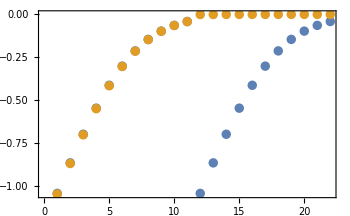

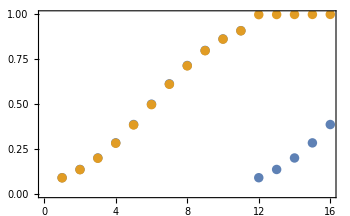

```mathematica
(*Log Space*)
ListPlot[Log10[{vRelData,dataArrayWithSSD[[1,3]]}]]
(*Real Space*)
ListPlot[{vRelData[[;;-7]],dataArrayWithSSD[[1,3,;;-7]]}]
```

### Parameter Distribution

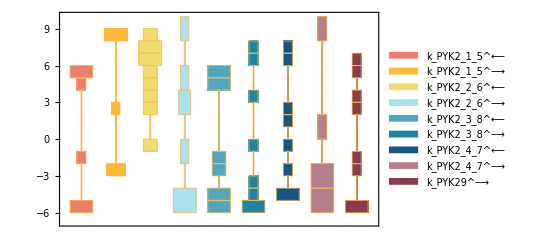

{((PYK2^c)_^+pep^c⇌(PYK2^c&pep^c)_^)^PYK21,((PYK2^c)_^+adp^c⇌(PYK2^c&adp^c)_^)^PYK22,((PYK2^c&atp^c)_^⇌(PYK2^c)_^+atp^c)^PYK23,((PYK2^c&pyr^c)_^⇌(PYK2^c)_^+pyr^c)^PYK24,((PYK2^c&adp^c)_^+pep^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK25,((PYK2^c&pep^c)_^+adp^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK26,((PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&atp^c)_^+pyr^c)^PYK27,((PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&pyr^c)_^+atp^c)^PYK28,((PYK2^c&pep^c&adp^c)_^⇌(PYK2^c&pyr^c&atp^c)_^)^PYK29}

```mathematica
DistributionChart[Transpose[Log10[finalDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Histogram*)
enzymeModel["Reactions"]
```

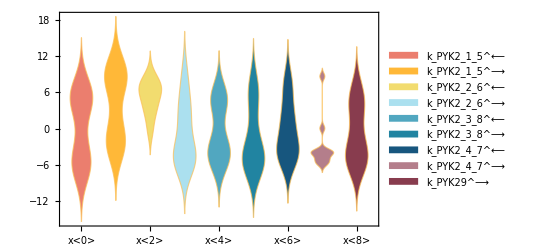

```mathematica
DistributionChart[Transpose[Log10[finalDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Parameter Analysis and Clustering

#### Remove Redundant Parameter Sets

```mathematica
logError = .5;
Needs["HierarchicalClustering`"]
distMat = DistanceMatrix[Log10[finalDataList[[All,2]]]];
cutoff = Length[finalDataList[[1,2]]]*logError^2;
positionsSimilar = Table[Flatten[Position[distMat[[i]],_?(0< #<cutoff&)]],{i,1,Length[distMat]}];
toRemove = {};
Do[
If[Length[Select[toRemove,#==i&]]==0,
toRemove = Flatten[Append[toRemove,positionsSimilar[[i]]]];],{i,1,Length[positionsSimilar]}];
toRemove = Union[toRemove];
finalDataListRed = finalDataList[[Complement[Table[i,{i,1,Length[finalDataList]}],toRemove]]];
```

#### Cluster Parameters

```mathematica
clusters=FindClusters[Log10[finalDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->2}}];(**)
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

### Data Error Distribution

```mathematica
errors=Table[vRelData[[i]]-finalDataList[[j,3,i]],{j,1,Length[finalDataList]},{i,1,Length[finalDataList[[1,3]]]}];
funcNames=Table[StringCases[func,RegularExpression["Development/(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}];
```

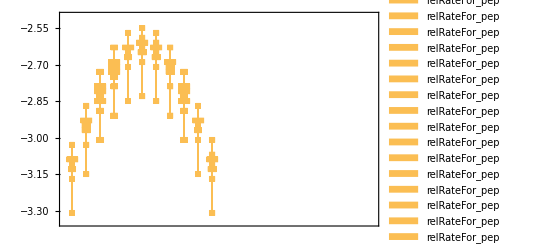

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames](*Histogram*)
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartLegends-> funcNames](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*);
```

## Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

### Solving for Km and kcat (using vKm = 1/2 Vmax approach)

```mathematica
paramFitSub=Thread[rateConstsSub[[All,1]]->bestFit[[2]]];
substrFor = rNonModelMets[getSubstrates[rxn]];
substrRev= rNonModelMets[getProducts[rxn]];
cosubsConc={parameter["cosub","amp[c]"]-> 0.001,parameter["cosub","adp[c]"]-> 0.002};
KeqVal=fittingData[[1,1]];
```

```mathematica
Forward Parameters;
vVal=Table[Simplify[absoluteRateForward/.Keq[getID[rxn]]->KeqVal/.{substrFor[[i]] -> substrFor[[i]],m_metabolite :> parameter["cosub", ToString@m]}/.paramFitSub/.cosubsConc[[i]]],{i,1,Length[substrFor]}];
vMax=Table[Limit[vVal[[i]],metSatForSub[[i]]],{i,1,Length[substrFor]}];
vKm=Table[Simplify[vVal[[i]] /. met :substrFor[[i]] :> Km[met, KeqName]],{i,1,Length[substrFor]}];
michMentSolForward = Table[Quiet[Solve[vKm[[i]]/vMax[[i]] == 1/2, Km[substrFor[[i]],KeqName]],{Solve::ratnz}],{i,1,Length[substrFor]}];
kcats={Table[rateconst["cat_"<>ToString[substrFor[[i,1]]],True]-> vMax[[i]]/.{parameter["E_total"]-> 1},{i,1,Length[vMax]}]};
michMentSolForward = Join[michMentSolForward,kcats]
```

{{{K_m_PYK^(adp^c)→1/(1.84086×10^6+6.09908×10^9 cosub_pep[c])2.69136×10^-68 (-1.56685×10^67-6.2917×10^71 cosub_pep[c]-1.71886×10^74 cosub_pep[c]^2-2.06961×10^15 √(8.48874×10^112+5.62359×10^116 cosub_pep[c]+9.31422×10^119 cosub_pep[c]^2+1.60304×10^119 cosub_pep[c]^3+6.89771×10^117 cosub_pep[c]^4))},{K_m_PYK^(adp^c)→1/(1.84086×10^6+6.09908×10^9 cosub_pep[c])2.69136×10^-68 (-1.56685×10^67-6.2917×10^71 cosub_pep[c]-1.71886×10^74 cosub_pep[c]^2+2.06961×10^15 √(8.48874×10^112+5.62359×10^116 cosub_pep[c]+9.31422×10^119 cosub_pep[c]^2+1.60304×10^119 cosub_pep[c]^3+6.89771×10^117 cosub_pep[c]^4))}},{{K_m_PYK^(pep^c)→-7.12999},{K_m_PYK^(pep^c)→0.000301955}},{k_cat_adp^⟶→(5.26761×10^-10 cosub_pep[c])/(0.000301826+1. cosub_pep[c]),k_cat_pep^⟶→9.74499×10^-11}}

```mathematica
Reverse Parameters;
vVal=Table[Simplify[absoluteRateReverse/.Keq[getID[rxn]]->KeqVal/.{substrRev[[i]] -> substrRev[[i]],m_metabolite :> parameter["cosub", ToString@m]}/.paramFitSub/.cosubsConc[[i]]],{i,1,Length[substrRev]}];
vMax=Table[Limit[vVal[[i]],metSatRevSub[[i]]],{i,1,Length[substrRev]}];
vKm=Table[Simplify[vVal[[i]] /. met :substrRev[[i]] :> Km[met, KeqName]],{i,1,Length[substrRev]}];
michMentSolReverse = Table[Quiet[Solve[vKm[[i]]/vMax[[i]] == 1/2, Km[substrRev[[i]],KeqName]],{Solve::ratnz}],{i,1,Length[substrRev]}];
kcats={Table[rateconst["cat_"<>ToString[substrRev[[i,1]]],True]-> vMax[[i]]/.{parameter["E_total"]-> 1},{i,1,Length[vMax]}]};
michMentSolReverse = Join[michMentSolReverse,kcats];

michMentParams=Flatten[Join[michMentSolForward,michMentSolReverse]];
michMentParams=Select[michMentParams,#[[2]]≥0&];
```

### Comparison to Published Values (*Change to Average +/- StdDev % Error for Each Param*)(*FIXME: Comparison to Published Values*)

```mathematica
michMentParams
```

{K_m_ADK1^(amp^c)→0.000044033,K_m_ADK1^(atp^c)→0.0000460316,k_cat_amp^⟶→1236.55,k_cat_atp^⟶→1239.38,K_m_ADK1^(adp^c)→0.000105475,k_cat_adp^⟶→319.003}

```mathematica
kmListFull[[All,1;;2]]
```

{{adp^c,0.000105},{atp^c,0.000046},{amp^c,0.000044}}

```mathematica
kcatList[[1]]
```

{{{adp,Null}},319.,1/S,7.4,40.}

```mathematica
MapThread[Append,{kcatList[[All,1,All,1]],kcatList[[All,2]]}]
```

{{adp,319.},{amp,atp,1296.}}

```mathematica
parameterData[[All,4]]
```

{Km,kcat,Km,Km,kcat}

```mathematica
"Published Values:"
publishedVals=Thread[michMentParams[[All,1]]->{KmAmp,KmAtp,kcatFor,kcatFor,KmAdp,kcatRev}]
"Fit Values:"
fitVals=michMentParams
Table[(Log10[publishedVals[[i,2]]]-Log10[fitVals[[i,2]]])^2,{i,1,Length[fitVals]}];
"Sum of Squared Log Errors:"
michMentSSE=Total[Table[(Log10[publishedVals[[i,2]]]-Log10[fitVals[[i,2]]])^2,{i,1,Length[fitVals]}]]
```

Published Values:

Thread::tdlen: Objects of unequal length in {InterpretationBox[K_m_StyleBox[ cannot be combined.

{K_m_ADK1^(amp^c),K_m_ADK1^(atp^c),K_m_ADK1^(adp^c)}→{KmAmp,KmAtp,kcatFor,kcatFor,KmAdp,kcatRev}

Fit Values:

{K_m_ADK1^(amp^c)→0.000044033,K_m_ADK1^(atp^c)→0.0000460316,K_m_ADK1^(adp^c)→0.000105475}

Part::partw: Part 3 of {InterpretationBox[K_m_StyleBox[ does not exist.

Sum of Squared Log Errors:

Part::partw: Part 3 of {InterpretationBox[K_m_StyleBox[ does not exist.

(4.33694+Log[KmAtp]/Log[10])^2+(4.35622+Log[K_m_ADK1^(atp^c)]/Log[10])^2+(3.97685+Log[({K_m_ADK1^(amp^c),K_m_ADK1^(atp^c),K_m_ADK1^(adp^c)}→{KmAmp,KmAtp,kcatFor,kcatFor,KmAdp,kcatRev})⟦3,2⟧]/Log[10])^2

{(20 atp^c f6p^c k_PFK11^⟵ k_PFK11^⟶ k_PFK12^⟵ k_PFK13^⟵ k_PFK13^⟶ k_PFK14^⟵ (k_PFK14^⟶ k_PFK15^⟶+((-1/2)^(2/5) k_PFK11^⟶ (k_PFK12^⟶)^2 k_PFK13^⟶ k_PFK14^⟶ k_PFK15^⟶)/(10 k_PFK11^⟵ k_PFK12^⟵ k_PFK13^⟵ k_PFK14^⟵)+k_PFK12^⟶ (k_PFK14^⟶+k_PFK15^⟶)) (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵)/((-1)^(2/5) 2^(3/5) f6p^c (k_PFK11^⟶)^2 (k_PFK12^⟶)^2 k_PFK13^⟶ (k_PFK13^⟵+atp^c k_PFK13^⟶) k_PFK14^⟶ k_PFK15^⟶ (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+20 (k_PFK11^⟵)^2 k_PFK12^⟵ k_PFK12^⟶ k_PFK13^⟵ k_PFK14^⟵ k_PFK14^⟶ (k_PFK13^⟵+k_PFK15^⟶) (gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵ (4 pep^c (k_PFK1_Inhibition_pep^⟵)^3 k_PFK1_Inhibition_pep^⟶ k_PFK1_TransitionStep^⟶+6 (pep^c)^2 (k_PFK1_Inhibition_pep^⟵)^2 (k_PFK1_Inhibition_pep^⟶)^2 k_PFK1_TransitionStep^⟶+4 (pep^c)^3 k_PFK1_Inhibition_pep^⟵ (k_PFK1_Inhibition_pep^⟶)^3 k_PFK1_TransitionStep^⟶+(pep^c)^4 (k_PFK1_Inhibition_pep^⟶)^4 k_PFK1_TransitionStep^⟶+(k_PFK1_Inhibition_pep^⟵)^4 (k_PFK1_TransitionStep^⟵+k_PFK1_TransitionStep^⟶)))+k_PFK11^⟵ k_PFK13^⟵ (20 f6p^c k_PFK11^⟶ k_PFK12^⟵ k_PFK14^⟵ (atp^c k_PFK13^⟶ k_PFK14^⟶ k_PFK15^⟶+k_PFK12^⟶ (k_PFK13^⟵ k_PFK14^⟶+k_PFK14^⟶ k_PFK15^⟶+atp^c k_PFK13^⟶ (k_PFK14^⟶+k_PFK15^⟶))) (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK12^⟶ k_PFK13^⟶ ((-1)^(2/5) 2^(3/5) k_PFK11^⟶ k_PFK12^⟶+20 atp^c k_PFK12^⟵ k_PFK14^⟵) k_PFK14^⟶ k_PFK15^⟶ (gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵ (4 pep^c (k_PFK1_Inhibition_pep^⟵)^3 k_PFK1_Inhibition_pep^⟶ k_PFK1_TransitionStep^⟶+6 (pep^c)^2 (k_PFK1_Inhibition_pep^⟵)^2 (k_PFK1_Inhibition_pep^⟶)^2 k_PFK1_TransitionStep^⟶+4 (pep^c)^3 k_PFK1_Inhibition_pep^⟵ (k_PFK1_Inhibition_pep^⟶)^3 k_PFK1_TransitionStep^⟶+(pep^c)^4 (k_PFK1_Inhibition_pep^⟶)^4 k_PFK1_TransitionStep^⟶+(k_PFK1_Inhibition_pep^⟵)^4 (k_PFK1_TransitionStep^⟵+k_PFK1_TransitionStep^⟶))))),(20 atp^c f6p^c k_PFK11^⟵ k_PFK11^⟶ k_PFK12^⟵ k_PFK13^⟵ k_PFK13^⟶ k_PFK14^⟵ (k_PFK14^⟶ k_PFK15^⟶+((-1/2)^(2/5) k_PFK11^⟶ (k_PFK12^⟶)^2 k_PFK13^⟶ k_PFK14^⟶ k_PFK15^⟶)/(10 k_PFK11^⟵ k_PFK12^⟵ k_PFK13^⟵ k_PFK14^⟵)+k_PFK12^⟶ (k_PFK14^⟶+k_PFK15^⟶)) (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵)/((-1)^(2/5) 2^(3/5) f6p^c (k_PFK11^⟶)^2 (k_PFK12^⟶)^2 k_PFK13^⟶ (k_PFK13^⟵+atp^c k_PFK13^⟶) k_PFK14^⟶ k_PFK15^⟶ (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+20 (k_PFK11^⟵)^2 k_PFK12^⟵ k_PFK12^⟶ k_PFK13^⟵ k_PFK14^⟵ k_PFK14^⟶ (k_PFK13^⟵+k_PFK15^⟶) (gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵ (4 pep^c (k_PFK1_Inhibition_pep^⟵)^3 k_PFK1_Inhibition_pep^⟶ k_PFK1_TransitionStep^⟶+6 (pep^c)^2 (k_PFK1_Inhibition_pep^⟵)^2 (k_PFK1_Inhibition_pep^⟶)^2 k_PFK1_TransitionStep^⟶+4 (pep^c)^3 k_PFK1_Inhibition_pep^⟵ (k_PFK1_Inhibition_pep^⟶)^3 k_PFK1_TransitionStep^⟶+(pep^c)^4 (k_PFK1_Inhibition_pep^⟶)^4 k_PFK1_TransitionStep^⟶+(k_PFK1_Inhibition_pep^⟵)^4 (k_PFK1_TransitionStep^⟵+k_PFK1_TransitionStep^⟶)))+k_PFK11^⟵ k_PFK13^⟵ (20 f6p^c k_PFK11^⟶ k_PFK12^⟵ k_PFK14^⟵ (atp^c k_PFK13^⟶ k_PFK14^⟶ k_PFK15^⟶+k_PFK12^⟶ (k_PFK13^⟵ k_PFK14^⟶+k_PFK14^⟶ k_PFK15^⟶+atp^c k_PFK13^⟶ (k_PFK14^⟶+k_PFK15^⟶))) (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK12^⟶ k_PFK13^⟶ ((-1)^(2/5) 2^(3/5) k_PFK11^⟶ k_PFK12^⟶+20 atp^c k_PFK12^⟵ k_PFK14^⟵) k_PFK14^⟶ k_PFK15^⟶ (gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵ (4 pep^c (k_PFK1_Inhibition_pep^⟵)^3 k_PFK1_Inhibition_pep^⟶ k_PFK1_TransitionStep^⟶+6 (pep^c)^2 (k_PFK1_Inhibition_pep^⟵)^2 (k_PFK1_Inhibition_pep^⟶)^2 k_PFK1_TransitionStep^⟶+4 (pep^c)^3 k_PFK1_Inhibition_pep^⟵ (k_PFK1_Inhibition_pep^⟶)^3 k_PFK1_TransitionStep^⟶+(pep^c)^4 (k_PFK1_Inhibition_pep^⟶)^4 k_PFK1_TransitionStep^⟶+(k_PFK1_Inhibition_pep^⟵)^4 (k_PFK1_TransitionStep^⟵+k_PFK1_TransitionStep^⟶)))))}